## MatLaB Import

### Init

#### Filesystem Setup

```mathematica
Clear[pathBase,pathSet,pathSubSet,pathSubSubSet,paths,nameSet,nameSubset,nameSubSubset]
pathBase=$HomeDirectory<>"/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/";
pathSet={"comb/","GeneralSkin/","IndividualSkin/FSkin/","IndividualSkin/JSkin/","IndividualSkin/NSkin/"};
pathSubSet={{""},{""},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"}};
pathSubSubSet = {{{""}},{{""}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}}};
paths=Table[Table[Table[pathBase<>pathSet[[i]]<>pathSubSet[[i,j]]<>pathSubSubSet[[i,j,k]]<>"mathematica/",{k,1,Length[pathSubSubSet[[i,j]]]}],{j,1,Length[pathSubSet[[i]]]}],{i,1,Length[pathSet]}];
nameSet={"RGB","RGB_GeneralSkin","RGB_FSkin","RGB_JSkin","RGB_NSkin"};
nameSubset = {{""},{""},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"}};
nameSubSubset = {{{""}},{{""}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}}};
```

```mathematica
Clear[setupFileSystem];
setupFileSystem[set_,subSet_,subSubSet_]:=Module[{temp1,temp2,temp3,temp4},
(* Set the path : path *)
(* and filenames : *)
(* filenames2D matLabNames2D names2D *)
(* filenames3D matLabNames3D names3D *)
(* NotebookDelete[temp1];NotebookDelete[temp2];NotebookDelete[temp3];NotebookDelete[temp4]; *)
path=paths[[set,subSet,subSubSet]];
temp1=Print["Set : ",nameSet[[set]],"     Subset : ",nameSubset[[set,subSet]],"     Subsubset : ",nameSubSubset[[set,subSet,subSubSet]]];
setupFileSystem[path];
]
setupFileSystem[pathIn_]:=Module[{temp1,temp2,temp3,temp4},
path=pathIn;
temp2=Print["path :",path];
AppendTo[$Path, path];
filenames2DTheta=Sort[StringReplace[FileNames["*Theta*CaCb*.mat",path],Evaluate[path]-> ""],StringLength[#1]<StringLength[#2]&];
filenames3DTheta=Sort[Complement[StringReplace[FileNames["*Theta*.mat",path],Evaluate[path]-> ""],filenames2DTheta],StringLength[#1]<StringLength[#2]&];
filenames2D=Sort[Complement[StringReplace[FileNames["*CaCb*.mat",path],Evaluate[path]-> ""],filenames2DTheta],StringLength[#1]<StringLength[#2]&];
filenames3D=Sort[Complement[StringReplace[FileNames[__~~".mat",path],Evaluate[path]-> ""],filenames2D,filenames2DTheta],StringLength[#1]<StringLength[#2]&];
len=Max[{Length[filenames3D],Length[filenames2D],Length[filenames3DTheta],Length[filenames2DTheta]}];
temp3=Print[TableForm[Transpose[Map[ArrayReshape[#,{len},""]&,{filenames3D,filenames2D,filenames3DTheta,filenames2DTheta}]],TableHeadings->{None,{"3D","2D","3D θ","2D θ"}}]];
matLabNames2D=StringReplace[filenames2D,".mat"->""];
matLabNames3D=StringReplace[filenames3D,".mat"->""];
matLabNames2DTheta=StringReplace[filenames2DTheta,".mat"->""];
matLabNames3DTheta=StringReplace[filenames3DTheta,".mat"->""];
names2D=StringReplace[matLabNames2D,"_"->""];
names3D=StringReplace[matLabNames3D,"_"->""];
names2DTheta=StringReplace[matLabNames2DTheta,"_"->""];
names3DTheta=StringReplace[matLabNames3DTheta,"_"->""];
temp4=Print[TableForm[Transpose[Map[ArrayReshape[#,{len},""]&,{matLabNames3D,names3D,matLabNames2D,names2D}]],TableHeadings->{None,{"3D MatLab","3D Mathematica","2D MatLab","2D Mathematica"}}]];
temp4=Print[TableForm[Transpose[Map[ArrayReshape[#,{len},""]&,{matLabNames3DTheta,names3DTheta,matLabNames2DTheta,names2DTheta}]],TableHeadings->{None,{"3D MatLab θ","3D Mathematica θ","2D MatLab θ","2D Mathematica θ"}}]];
]
```

#### Import Bins

```mathematica
fields={"name","axisNames","dims","nBins","bin","vals","bins","fBin","g","gMean","gSigma","gTheta","gAmp","aMin","aMax","aScale","count","a","subs","loc"};
```

```mathematica
Clear[ImportMatlabData];
betterImport[args__]:=Quiet[Import[args]/.{Transpose[Partition[{},_]]->0},{Partition::ilsmp}]
ImportMatlabData[name_,matLabName_,path_]:=Block[{indx},
Clear[Evaluate[Symbol[name]]];
Evaluate[Symbol[name]["name"]]=FromCharacterCode[(betterImport[(matLabName<>".mat"),{"Data","name"},Path->path])];
Evaluate[Symbol[name]["axisNames"]]=Map[("\""<>FromCharacterCode[#]<>"\"")&,(betterImport[(matLabName<>".mat"),{"Data","axisNames"},Path->path])];
Evaluate[Symbol[name]["dims"]]=(betterImport[(matLabName<>".mat"),{"Data","dims"},Path->path])[[1,1]];
Evaluate[Symbol[name]["nBins"]]=(betterImport[(matLabName<>".mat"),{"Data","nBins"},Path->path])[[1]];
indx=Table[i,{i,Symbol[name]["dims"],1,-1}]; indx[[-2]]=1; indx[[-1]]=2;Evaluate[Symbol[name]["bin"]]=Transpose[betterImport[(matLabName<>".mat"),{"Data","bin"},Path->path],indx];Evaluate[Symbol[name]["vals"]]=betterImport[(matLabName<>".mat"),{"Data","vals"},Path->path];Evaluate[Symbol[name]["bins"]]=betterImport[(matLabName<>".mat"),{"Data","bins"},Path->path];Evaluate[Symbol[name]["fBin"]]=Transpose[betterImport[(matLabName<>".mat"),{"Data","fBin"},Path->path],indx];Evaluate[Symbol[name]["g"]]=betterImport[(matLabName<>".mat"),{"Data","g"},Path->path];Evaluate[Symbol[name]["gMean"]]=(betterImport[(matLabName<>".mat"),{"Data","gMean"},Path->path])[[1]];Evaluate[Symbol[name]["gSigma"]]=(betterImport[(matLabName<>".mat"),{"Data","gSigma"},Path->path])[[1]];Evaluate[Symbol[name]["gTheta"]]=(betterImport[(matLabName<>".mat"),{"Data","gTheta"},Path->path])[[1,1]];Evaluate[Symbol[name]["gAmp"]]=(betterImport[(matLabName<>".mat"),{"Data","gAmp"},Path->path])[[1,1]];Evaluate[Symbol[name]["aMin"]]=(betterImport[(matLabName<>".mat"),{"Data","aMin"},Path->path])[[1]];Evaluate[Symbol[name]["aMax"]]=(betterImport[(matLabName<>".mat"),{"Data","aMax"},Path->path])[[1]];Evaluate[Symbol[name]["aScale"]]=Flatten[(betterImport[(matLabName<>".mat"),{"Data","aScale"},Path->path])];Evaluate[Symbol[name]["count"]]=(betterImport[(matLabName<>".mat"),{"Data","count"},Path->path])[[1,1]];Evaluate[Symbol[name]["a"]]=betterImport[(matLabName<>".mat"),{"Data","a"},Path->path];Evaluate[Symbol[name]["subs"]]=betterImport[(matLabName<>".mat"),{"Data","subs"},Path->path];Evaluate[Symbol[name]["loc"]]=betterImport[(matLabName<>".mat"),{"Data","loc"},Path->path];
If[Dimensions[Symbol[name]["fBin"]]==Dimensions[Symbol[name]["bin"]],
Print["All's Good"],
Message[ImportMatlabData::fBin,matLabName];
]
]
ImportMatlabData::fBin="The fBin in  `1` has not been normalised.";
```

### Set name and path to the matlab stats

```mathematica
setPath=pathBase;
TabView[{"Manual"->Panel[Column[{FileNameSetter[Dynamic[setPath],"Directory"],Dynamic[ setPath],Button["Set", setupFileSystem[setPath<>"/"]]}],Style["Manually Select the directory :",Large]],
Sequence@@(Table[nameSet[[i]]-> Column[{nameSet[[i]],
If[Length[nameSubset[[i]]]>1,
  TabView[ Table[nameSubset[[i,j]]-> Column[{nameSubset[[i,j]],
  If[Length[nameSubSubset[[i,j]]]>1,
     TabView[ Table[nameSubSubset[[i,j,k]]-> Column[{nameSubSubset[[i,j,k]],
     Button["Set",set=ii;subSet=jj;subSubSet=kk; setupFileSystem[ii,jj,kk]]/.{ii->i,jj-> j,kk->k}
     }],{k,1,Length[nameSubSubset[[i,j]]]}]],
     Button["Set",set=ii;subSet=jj;subSubSet=1; setupFileSystem[ii,jj,1]]/.{ii->i,jj-> j}
  ]
  }],{j,1,Length[nameSubset[[i]]]}] ],
   If[Length[nameSubSubset[[i,1]]]>1,
     TabView[ Table[nameSubSubset[[i,1,k]]-> Column[{nameSubSubset[[i,1,k]],
     Button["Set",set=ii;subSet=1;subSubSet=kk; setupFileSystem[ii,1,kk]]/.{ii->i,kk->k}
     }],{k,1,Length[nameSubSubset[[i,1]]]}]],
     Button["Set",set=ii;subSet=1;subSubSet=1; setupFileSystem[ii,1,1]]/.{ii->i}
  ]
]
}],{i,1,Length[nameSet]}])}]
```

123456

Import and Generate Data

### Init

```mathematica
title=StringReplace[matLabNames3D[[1]],{"RGB_"->"","_Bin"->""}]
```

Bin

Set the limit for the graphics

```mathematica
maxIncBins=2^16;
```

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

Whitepoint

Whitepoint

### Import and Generate Data

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

#### Generate the Plot Data

```mathematica
emptyTol = N[1/256];
While[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]>80000,emptyTol=2 emptyTol];
While[And[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]<40000,emptyTol>1/Symbol[name]["count"] ],emptyTol=emptyTol/2];
nIncBins=Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol];
pltCubeScale=Max[{Ceiling[N[nIncBins/maxIncBins]^(1/3)],1}];
Print["Bins included in plot : ",N[nIncBins/pltCubeScale^3]]
```

```mathematica
Symbol[name]["PlotRange"]=.
Symbol[name]["PlotLabel"]=.
Symbol[name]["PlotData"]=.
```

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Increase pltCubeScale or emptyTol to reduce the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

## 2. Skin the Bins

### Import and Generate Data

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin Skinned";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

#### Generate the Plot Data

```mathematica
emptyTol = N[1/256];
While[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]>80000,emptyTol=2 emptyTol];
While[And[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]<40000,emptyTol>1/Symbol[name]["count"] ],emptyTol=emptyTol/2];
nIncBins=Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol];
pltCubeScale=Max[{Ceiling[N[nIncBins/maxIncBins]^(1/3)],1}];
Print["Bins included in plot : ",N[nIncBins/pltCubeScale^3]]
```

```mathematica
Symbol[name]["PlotRange"]=.
Symbol[name]["PlotLabel"]=.
Symbol[name]["PlotData"]=.
```

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

## 3. Rotate the Bins

### Import and Generate Data

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

#### Generate the Plot Data

```mathematica
StringFreeQ[name,_~~"Rot"~~___]
```

```mathematica
emptyTol = N[1/256];
While[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]>80000,emptyTol=2 emptyTol];
While[And[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]<40000,emptyTol>1/Symbol[name]["count"] ],emptyTol=emptyTol/2];
nIncBins=Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol];
pltCubeScale=Max[{Ceiling[N[nIncBins/maxIncBins]^(1/3)],1}];
Print["Bins included in plot : ",N[nIncBins/pltCubeScale^3]]
```

```mathematica
Symbol[name]["PlotRange"]=.
Symbol[name]["PlotLabel"]=.
Symbol[name]["PlotData"]=.
```

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

## 4. Top and Tail the Bins

### Import and Generate Data

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin Topped and Tailed";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

#### Generate the Plot Data

```mathematica
emptyTol = N[1/256];
While[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]>80000,emptyTol=2 emptyTol];
While[And[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]<40000,emptyTol>1/Symbol[name]["count"] ],emptyTol=emptyTol/2];
nIncBins=Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol];
pltCubeScale=Max[{Ceiling[N[nIncBins/maxIncBins]^(1/3)],1}];
Print["Bins included in plot : ",N[nIncBins/pltCubeScale^3]]
```

```mathematica
Symbol[name]["PlotRange"]=.
Symbol[name]["PlotLabel"]=.
Symbol[name]["PlotData"]=.
```

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

## 5. Collapse the Bins

### Import and Generate Data

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca","Cb"};
Symbol[name]["PlotLabel"] = title<>" CaCb Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/256];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 6. Despeckle the Bins

### Import and Generate Data

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca","Cb"};
Symbol[name]["PlotLabel"] = title<>" CaCb Bin Despeckled";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

{Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2,Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1}

{BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}

### Import and Generate Data

#### Import Data

```mathematica
Do[
Print["Loading : "<>matLabNames[[i]]];
ImportMatlabData[names[[i]],matLabNames[[i]],path],
{i,1,Length[names]}]
```

Loading : Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2

All's Good

Loading : Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1

All's Good

Correct Axes names

```mathematica
Do[Symbol[names[[i]]]["axisNames"]={"Ca","Cb"},
{i,1,Length[names]}];
Do[
Symbol[names2D[[i]]]["PlotLabel"] = title<>" CaCb Bin Blob"<>ToString[i-2];,
{i,3,Length[names2D]}];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Saving : BinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Saving : BinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

Check the import

```mathematica
Do[Print[Row[{TableForm[Map[(Symbol[names[[i]]][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[names[[i]]][#]]})&,fields[[5;;8]]]]}]],
{i,1,Length[names]}]
```

name | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob2 | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 108.537 | 86.8571
gSigma | 6.25635 | 2.69955
gTheta | 0.931157 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 2.12091×10^8 | 
a | 118.588
104.268 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

name | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob1 | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 164.663 | 181.397
gSigma | 10.7802 | 0.957193
gTheta | 1.00761 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 3.83248×10^8 | 
a | 153.532
164.946 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
Do[
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[names[[i]]<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[names[[i]]],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[names[[i]]<>"[\"PlotRange\"]"]] = Transpose[{Symbol[names[[i]]]["aMin"],Symbol[names[[i]]]["aMax"]}];
Evaluate[ToExpression[names[[i]]<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[names[[i]]]["name"],"_"-> " "];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]],
{i,1,Length[names]}]
```

Set::setraw: Cannot assign to raw object "Bin CaCb Bin Blob1".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Set::setraw: Cannot assign to raw object "Bin CaCb Bin Blob2".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

Saving : BinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Saving : BinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

## 8. θ Rotate the Bins

```mathematica
blobNum=2;
```

```mathematica
theta=Symbol[names2D[[3]]]["gTheta"]
Symbol[names2D[[4]]]["gTheta"]
```

0.931157

1.00761

### Import and Generate Data

```mathematica
stage=1;
matLabName=matLabNames3DTheta[[stage]];
name=names3DTheta[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Theta_Rot

All's Good

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"L","Ca'","Cb'"};
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCa'Cb' Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin_Skinned +RGB_FSkin_Index_Pad_Bin_Skinned +RGB_FSkin_Index_Tip_Bin_Skinned +RGB_FSkin_Thumb_Pad_Bin_Skinned +RGB_FSkin_Thumb_Tip_Bin_Skinned +RGB_JSkin_Bin_Skinned +RGB_JSkin_Index_Pad_Bin_Skinned +RGB_JSkin_Index_Tip_Bin_Skinned +RGB_JSkin_Thumb_Pad_Bin_Skinned +RGB_JSkin_Thumb_Tip_Bin_Skinned +RGB_NSkin_Bin_Skinned +RGB_NSkin_Index_Pad_Bin_Skinned +RGB_NSkin_Index_Tip_Bin_Skinned +RGB_NSkin_Thumb_Pad_Bin_Skinned +RGB_NSkin_Thumb_Tip_Bin_Skinned |  | 
axisNames | L | Ca' | Cb'
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | 0 |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 256. | 256. | 256.
aScale | 256. | 256. | 256.
count | 7.47299×10^8 |  | 
a | 0 |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
257
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
StringFreeQ[name,_~~"Rot"~~___]
```

False

```mathematica
emptyTol = N[1/256];
While[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]>80000,emptyTol=2 emptyTol];
While[And[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]<40000,emptyTol>1/Symbol[name]["count"] ],emptyTol=emptyTol/2];
nIncBins=Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol];
pltCubeScale=Max[{Ceiling[N[nIncBins/maxIncBins]^(1/3)],1}];
Print["Bins included in plot : ",N[nIncBins/pltCubeScale^3]]
```

Bins included in plot : 62327.

```mathematica
Symbol[name]["PlotRange"]=.
Symbol[name]["PlotLabel"]=.
Symbol[name]["PlotData"]=.
```

Unset::norep: Assignment on BinThetaRot for BinThetaRot["PlotRange"] not found.

$Failed

Unset::norep: Assignment on BinThetaRot for BinThetaRot["PlotLabel"] not found.

$Failed

Unset::norep: Assignment on BinThetaRot for BinThetaRot["PlotData"] not found.

$Failed

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale,theta],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale,theta]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Increase pltCubeScale or emptyTol to reduce the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Theta_Rot_Animation/" already exists.

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Theta_Rot_Animation/Bin_Theta_Rot.gif

## 9. θ Top and Tail the Bins

### Import and Generate Data

```mathematica
stage=2;
matLabName=matLabNames3DTheta[[stage]];
name=names3DTheta[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Theta_Rot_TopTail

All's Good

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"L","Ca'","Cb'"};
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCa'Cb' Bin Topped and Tailed";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | Bin_Theta_Rot_TopTail |  | 
axisNames | L | Ca' | Cb'
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | 0 |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 256. | 256. | 256.
aScale | 256. | 256. | 256.
count | 7.09205×10^8 |  | 
a | 0 |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
257
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
emptyTol = N[1/256];
While[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]>80000,emptyTol=2 emptyTol];
While[And[Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol]<40000,emptyTol>1/Symbol[name]["count"] ],emptyTol=emptyTol/2];
nIncBins=Count[Flatten[Symbol[name]["fBin"]],n_/;n>emptyTol];
pltCubeScale=Max[{Ceiling[N[nIncBins/maxIncBins]^(1/3)],1}];
Print["Bins included in plot : ",N[nIncBins/pltCubeScale^3]]
```

Bins included in plot : 60024.

```mathematica
Symbol[name]["PlotRange"]=.
Symbol[name]["PlotLabel"]=.
Symbol[name]["PlotData"]=.
```

Unset::norep: Assignment on BinThetaRotTopTail for BinThetaRotTopTail["PlotRange"] not found.

$Failed

Unset::norep: Assignment on BinThetaRotTopTail for BinThetaRotTopTail["PlotLabel"] not found.

$Failed

Unset::norep: Assignment on BinThetaRotTopTail for BinThetaRotTopTail["PlotData"] not found.

$Failed

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale,theta],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale,theta]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Increase pltCubeScale or emptyTol to reduce the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Theta_Rot_TopTail_Animation/" already exists.

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Theta_Rot_TopTail_Animation/Bin_Theta_Rot_TopTail.gif

## 10. θ Collapse the Bins

### Import and Generate Data

```mathematica
stage=1;
matLabName=matLabNames2DTheta[[stage]];
name=names2DTheta[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Theta_Rot_TopTail_CaCb

All's Good

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca'","Cb'"};
Symbol[name]["PlotLabel"] = title<>" CaCb Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | Bin_Theta_Rot_TopTail_bc | 
axisNames | Ca' | Cb'
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 0. | 0.
gSigma | 0. | 0.
gTheta | 0. | 
gAmp | 1. | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 7.09205×10^8 | 
a | 0 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/256];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale,theta];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin CaCb Bin".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 11. θ Despeckle the Bins

### Import and Generate Data

```mathematica
stage=2;
matLabName=matLabNames2DTheta[[2]];
name=names2DTheta[[2]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Theta_Rot_TopTail_CaCb_Despec

All's Good

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca'","Cb'"};
Symbol[name]["PlotLabel"] = title<>" Ca'Cb' Bin Despeckled";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | Bin_Theta_Rot_TopTail_bc | 
axisNames | Ca' | Cb'
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 0. | 0.
gSigma | 0. | 0.
gTheta | 0. | 
gAmp | 1. | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 7.09205×10^8 | 
a | 0 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale,theta];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin Ca'Cb' Bin Despeckled".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 12. θ Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2DTheta[[stage-4;;]]
names=names2DTheta[[stage-4;;]]
```

{Bin_Theta_Rot_TopTail_CaCb_Despec_blob2,Bin_Theta_Rot_TopTail_CaCb_Despec_blob1}

{BinThetaRotTopTailCaCbDespecblob2,BinThetaRotTopTailCaCbDespecblob1}

### Import and Generate Data

#### Import Data

```mathematica
Do[
Print["Loading : "<>matLabNames[[i]]];
ImportMatlabData[names[[i]],matLabNames[[i]],path],
{i,1,Length[names]}]
```

Loading : Bin_Theta_Rot_TopTail_CaCb_Despec_blob2

All's Good

Loading : Bin_Theta_Rot_TopTail_CaCb_Despec_blob1

All's Good

Correct Axes names

```mathematica
Do[Symbol[names[[i]]]["axisNames"]={"Ca'","Cb'"},
{i,1,Length[names]}];
Do[
Symbol[names2DTheta[[i]]]["PlotLabel"] = title<>" Ca'Cb' Bin Blob"<>ToString[i-2];,
{i,3,Length[names2DTheta]}];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Saving : BinThetaRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb_Despec_blob2.m

Saving : BinThetaRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb_Despec_blob1.m

Check the import

```mathematica
Do[Print[Row[{TableForm[Map[(Symbol[names[[i]]][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[names[[i]]][#]]})&,fields[[5;;8]]]]}]],
{i,1,Length[names]}]
```

name | Bin_Theta_Rot_TopTail_bc blob2 | 
axisNames | Ca' | Cb'
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 90.7396 | 123.156
gSigma | 6.82998 | 3.08842
gTheta | -1.71932 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 1.78262×10^8 | 
a | 92.1342
123.542 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

name | Bin_Theta_Rot_TopTail_bc blob1 | 
axisNames | Ca' | Cb'
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 175.698 | 127.374
gSigma | 8.06256 | 1.34934
gTheta | 1.50481 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 4.50677×10^8 | 
a | 170.978
125.918 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
Do[
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[names[[i]]<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[names[[i]]],"LCaCb",emptyTol,pltCubeScale,theta];
Evaluate[ToExpression[names[[i]]<>"[\"PlotRange\"]"]] = Transpose[{Symbol[names[[i]]]["aMin"],Symbol[names[[i]]]["aMax"]}];
Evaluate[ToExpression[names[[i]]<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[names[[i]]]["name"],"_"-> " "];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]],
{i,1,Length[names]}]
```

Set::setraw: Cannot assign to raw object "Bin Ca'Cb' Bin Blob1".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Set::setraw: Cannot assign to raw object "Bin Ca'Cb' Bin Blob2".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

Saving : BinThetaRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb_Despec_blob2.m

Saving : BinThetaRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb_Despec_blob1.m

Generate the Plot Notebook

## 0. Init

```mathematica
title=StringReplace[matLabNames3D[[1]],{"RGB_"->"","_Bin"->""}];
```

```mathematica
outputNotebook=path<>matLabNames3D[[1]]<>"_plots.nb"
nb=CreateDocument[];
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_plots.nb

```mathematica
outNames = {"Fill","Skin","Rotate","TopnTail","Collapse","Despeckle","Blobs","Fit","Export"};
figNames = {"Fill_the_Bins","Skin_the_Bins","Rotate_the_Bins","Top_and_Tail_the_Bins","Collapse_the_Bins","Despeckle_the_Bins","Find_the_Blobs","Fit_the_Gaussian","Export"};
figPath = path<>"Figs/";
CreateDirectory[figPath];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Figs/" already exists.

```mathematica
NotebookWrite[nb,Cell[title,"Chapter"]]
```

```mathematica
NotebookWrite[nb,Cell["Init","Section"]]
NotebookDefinitionWrite[nb,"path"]
NotebookDefinitionWrite[nb,"figPath"]
NotebookDefinitionWrite[nb,"figNames"]
NotebookDefinitionWrite[nb,"filenames2D"]
NotebookDefinitionWrite[nb,"matLabNames2D"]
NotebookDefinitionWrite[nb,"names2D"]
NotebookDefinitionWrite[nb,"filenames3D"]
NotebookDefinitionWrite[nb,"matLabNames3D"]
NotebookDefinitionWrite[nb,"names3D"]
(* 
Possibly add function definitions to the oputput.

Map[NotebookDefinitionWrite[nb,#]&,{"LCaCbColorFast","SetUpLCaCbColor","HistoPlot3D","boundBox","skinnedBox","topAndTailBox","projectedView","GaussianFitFun","μσθFromBin","GaussianFit","MajorMinorAxesPoints","dataRange","elipsePlt","fitXPlt","fitYPlt","statTable","fit2DLinesPlt","fit2DAnglePlt","fitComparisonPlt","overlayElems","gFitElems"}]
*)
```

```mathematica
NotebookSave[nb,outputNotebook]
```

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

Bin

Bin

### Generate the Plot Notebook

```mathematica
stage=1;
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin";
```

```mathematica
Symbol[names3D[[stage]]]["PlotLabel"]
```

Bin RGB Bin

```mathematica
stage=1;
NotebookWrite[nb,Cell["1. Fill the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
```

NotebookWrite[nb,Cell[1. Fill the Bins,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[1]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin.m",],;}]],Input]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " LCaCb Bin\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{Bin,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> LCaCb Bin"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{Bin,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{Bin,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{Bin,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{Bin,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin.m",,,"Bin"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"SaveDefinitions","→","True"}]}],"]"}],"
"}]],"Code"]]
```

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{Manipulate,[,
,RowBox[{RowBox[{Graphics3D,[,RowBox[{RowBox[{Bin,[,"PlotData",]}],,,
,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewAngle,→,RowBox[{Pi,/,7}]}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{Bin,[,"axisNames",]}]}],,,RowBox[{ImagePadding,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{2,,,2}],}}],,,RowBox[{{,RowBox[{2,,,2}],}}]}],}}]}],,,RowBox[{ImageSize,→,400}],,,RowBox[{ImageMargins,→,2}],,,RowBox[{PlotRange,→, ,RowBox[{Bin,[,"PlotRange",]}]}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,, ,0}],}}]}],,,RowBox[{PlotLabel,→, ,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Bin,[,"PlotLabel",]}],,,RowBox[{Row,[,RowBox[{{,RowBox[{"θ = ",,,θ,,,"    ϕ = ",,,ϕ}],}}],]}]}],}}],]}]}]}],]}],
,,,RowBox[{{,RowBox[{RowBox[{{,RowBox[{θ,,,0}],}}],,,0,,,RowBox[{Pi,/,2}],,,RowBox[{Pi,/,48}]}],}}],,,RowBox[{{,RowBox[{RowBox[{{,RowBox[{ϕ,,,RowBox[{Pi,/,3}]}],}}],,,0,,,RowBox[{Pi,/,2}],,,RowBox[{Pi,/,48}]}],}}],,,RowBox[{SaveDefinitions,→,True}]}],]}],
}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

NotebookWrite[nb,Cell[Show the animation,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{animation,=,RowBox[{ListAnimate,[,RowBox[{BinFrames,,,RowBox[{AnimationDirection,→,ForwardBackward}]}],]}]}]],Code]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"5",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"5",RowBox[{"Pi","/","12"}]}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView"  ,"=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView" ,"=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 1 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 1 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 1 ⟧.

Part::partd: Part specification outNames ⟦ 1 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 1 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦1⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{θ,=,RowBox[{5,RowBox[{Pi,/,48}]}]}],,,RowBox[{ϕ,=,RowBox[{5,RowBox[{Pi,/,12}]}]}],,,isoView,,,redView,,,greenView,,,blueView,,,RowBox[{skinDepth,=,9}]}],}}],,,RowBox[{RowBox[{isoView,=,RowBox[{Rasterize,[,RowBox[{Graphics3D,[,RowBox[{RowBox[{Bin,[,"PlotData",]}],,,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{Bin,[,"axisNames",]}]}],,,RowBox[{ImageSize,→,400}]}],]}],]}]}],;,
,RowBox[{redView,=,RowBox[{projectedView,[,RowBox[{Bin,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,Bin,]}],,,RowBox[{skinnedBox,[,RowBox[{Bin,,,skinDepth}],]}]}],}}],,,1}],]}]}],;,
,RowBox[{greenView,=,RowBox[{projectedView,[,RowBox[{Bin,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,Bin,]}],,,RowBox[{skinnedBox,[,RowBox[{Bin,,,skinDepth}],]}]}],}}],,,2}],]}]}],;,
,RowBox[{blueView,=,RowBox[{projectedView,[,RowBox[{Bin,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,Bin,]}],,,RowBox[{skinnedBox,[,RowBox[{Bin,,,skinDepth}],]}]}],}}],,,3}],]}]}],;,
,RowBox[{GraphicsGrid,[,RowBox[{{,RowBox[{RowBox[{{,RowBox[{isoView,,,redView}],}}],,,RowBox[{{,RowBox[{greenView,,,blueView}],}}]}],}}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦1⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Fill_the_Bins.jpg"}],,,title<>out<>outNames⟦1⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Fill_the_Bins.eps"}],,,title<>out<>outNames⟦1⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Fill_the_Bins.pdf"}],,,title<>out<>outNames⟦1⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 2. Skin the Bins

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin Skinned";
```

### Generate the Plot Notebook

```mathematica
stage=2;
NotebookWrite[nb,Cell["2. Skin the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[2]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

NotebookWrite[nb,Cell[2. Skin the Bins,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " LCaCb Bin\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinSkinned,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> LCaCb Bin"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinSkinned,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinSkinned,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinSkinned,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinSkinned,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned.m",,,"BinSkinned"}],]}]}],]}]}],}}],]}],]}]],Code]]

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[Show the animation,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{animation,=,RowBox[{ListAnimate,[,RowBox[{BinSkinnedFrames,,,RowBox[{AnimationDirection,→,ForwardBackward}]}],]}]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the Projected views,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{"imgSz","=","600"}],";"}],"\n",
RowBox[{RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"5",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"5",RowBox[{"Pi","/","12"}]}]}],",",RowBox[{"skinDepth","=","9"}],",","redView",",","greenView",",","blueView",",","redViewSkinned",",","greenViewSkinned",",","blueViewSkinned"}],"}"}],",","\n",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[","\n",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[2]],"[","\"\<PlotData\>\"","]"}],",","\n",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",","\n",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[2]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[1]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[1]],",","skinDepth"}],"]"}]}],"}"}],",","1",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[1]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[1]],",","skinDepth"}],"]"}]}],"}"}],",",RowBox[{"-","2"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[1]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[1]],",","skinDepth"}],"]"}]}],"}"}],",","3",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"redViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3D[[2]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[2]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[2]],",","skinDepth"}],"]"}]}],"}"}],",","1",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"greenViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3D[[2]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[2]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[2]],",","skinDepth"}],"]"}]}],"}"}],",",RowBox[{"-","2"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"blueViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3D[[2]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[2]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[2]],",","skinDepth"}],"]"}]}],"}"}],",","3",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[2]],"=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","\n",RowBox[{title<>"out"<>outNames[[2]]<>"Triple","=",RowBox[{"Panel","[",RowBox[{"Grid","[",RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{"isoView",",","\"\<The Skinned RGB Bins\>\"",",",RowBox[{"Background","→","White"}]}],"]"}],",","\n",RowBox[{"Panel","[",RowBox[{RowBox[{"GraphicsColumn","[",RowBox[{RowBox[{"{",RowBox[{"redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{"imgSz","/","3"}],"]"}],",","imgSz"}],"}"}]}]}],"]"}],",","\"\<Before\>\"",",",RowBox[{"Background","→","White"}]}],"]"}],",","\n",RowBox[{"Panel","[",RowBox[{RowBox[{"GraphicsColumn","[",RowBox[{RowBox[{"{",RowBox[{"redViewSkinned",",","greenViewSkinned",",","blueViewSkinned"}],"}"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{"imgSz","/","3"}],"]"}],",","imgSz"}],"}"}]}]}],"]"}],",","\"\<After Skinning\>\"",",",RowBox[{"Background","→","White"}]}],"]"}]}],"}"}],"}"}],"]"}],"]"}]}],";"}]}],"
","]"}],";"}],"\n",RowBox[{"TabView","[",RowBox[{"{","\n",
RowBox[{RowBox[{"\"\<Equal\>\"","->",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{title<>"out"<>outNames[[2]],",",RowBox[{"Background","->","White"}],",",RowBox[{"ImageSize","→",RowBox[{RowBox[{"(",RowBox[{"2","+","0.1"}],")"}]," ",RowBox[{"(","1.1",")"}],"imgSz"}]}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",RowBox[{RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Skin_the_Bins.jpg\>\""}],",",title<>"out"<>outNames[[2]],",",RowBox[{"ImageResolution","->","300"}]}],"]"}],";","\n",RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Skin_the_Bins.eps\>\""}],",",title<>"out"<>outNames[[2]]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Skin_the_Bins.pdf\>\""}],",",title<>"out"<>outNames[[2]]}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]}],","," ","\n",
RowBox[{"\"\<Triple\>\"","→"," ",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{title<>"out"<>outNames[[2]]<>"Triple",",",RowBox[{"Background","->","White"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{"1","+",RowBox[{"2","/","3"}],"+","0.2"}],")"}]," ","imgSz"}],",",RowBox[{RowBox[{"(","1.2",")"}]," ","imgSz"}]}],"}"}]}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",RowBox[{RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Skin_the_Bins.jpg\>\""}],",",title<>"out"<>outNames[[2]]<>"Triple",",",RowBox[{"ImageResolution","->","300"}]}],"]"}],";","\n",RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Skin_the_Bins.eps\>\""}],",",title<>"out"<>outNames[[2]]<>"Triple"}],"]"}],";","\n",RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Skin_the_Bins.pdf\>\""}],",",title<>"out"<>outNames[[2]]<>"Triple"}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]}]}],"\n","}"}],"]"}]}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 2 ⟧.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧ <> "Triple".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{imgSz,=,600}],;}],
,RowBox[{RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{θ,=,RowBox[{5,RowBox[{Pi,/,48}]}]}],,,RowBox[{ϕ,=,RowBox[{5,RowBox[{Pi,/,12}]}]}],,,RowBox[{skinDepth,=,9}],,,redView,,,greenView,,,blueView,,,redViewSkinned,,,greenViewSkinned,,,blueViewSkinned}],}}],,,
,RowBox[{RowBox[{isoView,=,RowBox[{Rasterize,[,
,RowBox[{Graphics3D,[,RowBox[{RowBox[{BinSkinned,[,"PlotData",]}],,,
,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,
,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{BinSkinned,[,"axisNames",]}]}],,,RowBox[{ImageSize,→,imgSz}]}],]}],]}]}],;,
,RowBox[{redView,=,RowBox[{projectedView,[,RowBox[{Bin,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,Bin,]}],,,RowBox[{skinnedBox,[,RowBox[{Bin,,,skinDepth}],]}]}],}}],,,1,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{greenView,=,RowBox[{projectedView,[,RowBox[{Bin,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,Bin,]}],,,RowBox[{skinnedBox,[,RowBox[{Bin,,,skinDepth}],]}]}],}}],,,RowBox[{-,2}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{blueView,=,RowBox[{projectedView,[,RowBox[{Bin,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,Bin,]}],,,RowBox[{skinnedBox,[,RowBox[{Bin,,,skinDepth}],]}]}],}}],,,3,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{redViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinSkinned,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinned,]}],,,RowBox[{skinnedBox,[,RowBox[{BinSkinned,,,skinDepth}],]}]}],}}],,,1,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{greenViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinSkinned,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinned,]}],,,RowBox[{skinnedBox,[,RowBox[{BinSkinned,,,skinDepth}],]}]}],}}],,,RowBox[{-,2}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{blueViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinSkinned,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinned,]}],,,RowBox[{skinnedBox,[,RowBox[{BinSkinned,,,skinDepth}],]}]}],}}],,,3,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦2⟧,=,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{isoView,,,redView}],}}],,,RowBox[{{,RowBox[{greenView,,,blueView}],}}]}],}}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦2⟧<>Triple,=,RowBox[{Panel,[,RowBox[{Grid,[,RowBox[{{,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{isoView,,,"The Skinned RGB Bins",,,RowBox[{Background,→,White}]}],]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{GraphicsColumn,[,RowBox[{RowBox[{{,RowBox[{redView,,,greenView,,,blueView}],}}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{N,[,RowBox[{imgSz,/,3}],]}],,,imgSz}],}}]}]}],]}],,,"Before",,,RowBox[{Background,→,White}]}],]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{GraphicsColumn,[,RowBox[{RowBox[{{,RowBox[{redViewSkinned,,,greenViewSkinned,,,blueViewSkinned}],}}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{N,[,RowBox[{imgSz,/,3}],]}],,,imgSz}],}}]}]}],]}],,,"After Skinning",,,RowBox[{Background,→,White}]}],]}]}],}}],}}],]}],]}]}],;}]}],
,]}],;}],
,RowBox[{TabView,[,RowBox[{{,
,RowBox[{RowBox[{"Equal",->,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧,,,RowBox[{Background,->,White}],,,RowBox[{ImageSize,→,RowBox[{RowBox[{(,RowBox[{2,+,0.1}],)}], ,RowBox[{(,1.1,)}],imgSz}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.jpg"}],,,title<>out<>outNames⟦2⟧,,,RowBox[{ImageResolution,->,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.eps"}],,,title<>out<>outNames⟦2⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.pdf"}],,,title<>out<>outNames⟦2⟧}],]}]}]}],]}]}],}}],]}],]}]}],,, ,
,RowBox[{"Triple",→, ,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧<>Triple,,,RowBox[{Background,->,White}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{1,+,RowBox[{2,/,3}],+,0.2}],)}], ,imgSz}],,,RowBox[{RowBox[{(,1.2,)}], ,imgSz}]}],}}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.jpg"}],,,title<>out<>outNames⟦2⟧<>Triple,,,RowBox[{ImageResolution,->,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.eps"}],,,title<>out<>outNames⟦2⟧<>Triple}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.pdf"}],,,title<>out<>outNames⟦2⟧<>Triple}],]}]}]}],]}]}],}}],]}],]}]}]}],
,}}],]}]}],Code]]

## 3. Rotate the Bins

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin";
```

### Generate the Plot Notebook

```mathematica
stage=3;
NotebookWrite[nb,Cell["3. Rotate the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[3]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[3. Rotate the Bins,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " LCaCb Bin\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinThetaRot,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> LCaCb Bin"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRot,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRot,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRot,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRot,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot.m",,,"BinThetaRot"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the animation,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

NotebookWrite[nb,Cell[BoxData[RowBox[{animation,=,RowBox[{ListAnimate,[,RowBox[{BinThetaRotFrames,,,RowBox[{AnimationDirection,→,ForwardBackward}]}],]}]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"SaveDefinitions","→","True"}]}],"]"}],"
"}]],"Code"]]
```

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{Manipulate,[,
,RowBox[{RowBox[{Graphics3D,[,RowBox[{RowBox[{BinThetaRot,[,"PlotData",]}],,,
,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewAngle,→,RowBox[{Pi,/,7}]}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{BinThetaRot,[,"axisNames",]}]}],,,RowBox[{ImagePadding,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{2,,,2}],}}],,,RowBox[{{,RowBox[{2,,,2}],}}]}],}}]}],,,RowBox[{ImageSize,→,400}],,,RowBox[{ImageMargins,→,2}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRot,[,"PlotRange",]}]}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,, ,0}],}}]}],,,RowBox[{PlotLabel,→, ,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{BinThetaRot,[,"PlotLabel",]}],,,RowBox[{Row,[,RowBox[{{,RowBox[{"θ = ",,,θ,,,"    ϕ = ",,,ϕ}],}}],]}]}],}}],]}]}]}],]}],
,,,RowBox[{{,RowBox[{RowBox[{{,RowBox[{θ,,,0}],}}],,,0,,,RowBox[{Pi,/,2}],,,RowBox[{Pi,/,48}]}],}}],,,RowBox[{{,RowBox[{RowBox[{{,RowBox[{ϕ,,,RowBox[{Pi,/,3}]}],}}],,,0,,,RowBox[{Pi,/,2}],,,RowBox[{Pi,/,48}]}],}}],,,RowBox[{SaveDefinitions,→,True}]}],]}],
}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the Projected views,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}],",",RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{"boundBox","[",names3D[[stage]],"]"}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 3 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 3 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 3 ⟧.

Part::partd: Part specification outNames ⟦ 3 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 3 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦3⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{depth,=,depth}],,,RowBox[{θ,=,RowBox[{7,RowBox[{Pi,/,48}]}]}],,,RowBox[{ϕ,=,RowBox[{Pi,/,3}]}],,,isoView,,,redView,,,greenView,,,blueView}],}}],,,RowBox[{RowBox[{isoView,=,RowBox[{Rasterize,[,RowBox[{Graphics3D,[,RowBox[{RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}],,,RowBox[{BinThetaRot,[,"PlotData",]}]}],}}],,,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,,0}],}}]}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{BinThetaRot,[,"axisNames",]}]}],,,RowBox[{ImageSize,→,400}],,,RowBox[{Lighting,→,"Neutral"}]}],]}],]}]}],;,
,RowBox[{redView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{boundBox,[,BinThetaRot,]}],}}],,,1}],]}]}],;,
,RowBox[{greenView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,2}],]}]}],;,
,RowBox[{blueView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,3}],]}]}],;,
,RowBox[{GraphicsGrid,[,RowBox[{{,RowBox[{RowBox[{{,RowBox[{isoView,,,redView}],}}],,,RowBox[{{,RowBox[{greenView,,,blueView}],}}]}],}}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦3⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Rotate_the_Bins.jpg"}],,,title<>out<>outNames⟦3⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Rotate_the_Bins.eps"}],,,title<>out<>outNames⟦3⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Rotate_the_Bins.pdf"}],,,title<>out<>outNames⟦3⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 4. Top and Tail the Bins

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin Topped and Tailed";
```

### Generate the Plot Notebook

```mathematica
stage=4;
depth=42;
NotebookWrite[nb,Cell["4. Top and Tail the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[2]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin Topped and Tailed"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

NotebookWrite[nb,Cell[4. Top and Tail the Bins,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " LCaCb Bin Topped and Tailed\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinSkinnedRot,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> LCaCb Bin Topped and Tailed"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinSkinnedRot,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinSkinnedRot,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinSkinnedRot,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinSkinnedRot,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot.m",,,"BinSkinnedRot"}],]}]}],]}]}],}}],]}],]}]],Code]]

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[Show the animation,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{animation,=,RowBox[{ListAnimate,[,RowBox[{BinSkinnedRotFrames,,,RowBox[{AnimationDirection,→,ForwardBackward}]}],]}]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the Projected views,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{
RowBox[{"imgSz","=","600"}],";"}],"\n",
RowBox[{RowBox[{"Block","[",RowBox[{RowBox[{"{",
RowBox[{RowBox[{"θ","=",RowBox[{"5",RowBox[{"Pi","/","48"}]}]}],",",
RowBox[{"ϕ","=",RowBox[{"5",RowBox[{"Pi","/","12"}]}]}],",",
RowBox[{"depth","=","42"}]}],"}"}],",","\n",
RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[","\n",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",","\n",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}],",",RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",","\n",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",","\n",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",","\n",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","imgSz"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage-1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage-1]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage-1]],",","depth"}],"]"}]}],"}"}],",","1",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage-1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage-1]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage-1]],",","depth"}],"]"}]}],"}"}],",",RowBox[{"-","2"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage-1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage-1]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage-1]],",","depth"}],"]"}]}],"}"}],",","3",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"redViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","1",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"greenViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",",RowBox[{"-","2"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"blueViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","3",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","\n",
RowBox[{title<>"out"<>outNames[[stage]]<>"Triple","=",RowBox[{"Panel","[",RowBox[{"Grid","[",RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{"isoView",",","\"\<The Skinned RGB Bins\>\"",",",RowBox[{"Background","→","White"}]}],"]"}],",","\n",
RowBox[{"Panel","[",RowBox[{RowBox[{"GraphicsColumn","[",RowBox[{RowBox[{"{",RowBox[{"redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{"imgSz","/","3"}],"]"}],",","imgSz"}],"}"}]}]}],"]"}],",","\"\<Before\>\"",",",RowBox[{"Background","→","White"}]}],"]"}],",","\n",
RowBox[{"Panel","[",RowBox[{RowBox[{"GraphicsColumn","[",RowBox[{RowBox[{"{",RowBox[{"redViewSkinned",",","greenViewSkinned",",","blueViewSkinned"}],"}"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{"imgSz","/","3"}],"]"}],",","imgSz"}],"}"}]}]}],"]"}],",","\"\<After Top&Tailing\>\"",",",RowBox[{"Background","→","White"}]}],"]"}]}],"}"}],"}"}],"]"}],"]"}]}],";"}]}],"
","]"}],";"}],"\n",
RowBox[{"TabView","[",RowBox[{"{","\n",
RowBox[{RowBox[{"\"\<Equal\>\"","->",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{title<>"out"<>outNames[[stage]],",",RowBox[{"Background","->","White"}],",",RowBox[{"ImageSize","→",RowBox[{RowBox[{"(",RowBox[{"2","+","0.1"}],")"}]," ",RowBox[{"(","1.1",")"}],"imgSz"}]}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",
RowBox[{RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.jpg\>\""}],",",title<>"out"<>outNames[[stage]],",",RowBox[{"ImageResolution","->","300"}]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.eps\>\""}],",",title<>"out"<>outNames[[stage]]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.pdf\>\""}],",",title<>"out"<>outNames[[stage]]}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]}],","," ","\n",
RowBox[{"\"\<Triple\>\"","→"," ",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{title<>"out"<>outNames[[stage]]<>"Triple",",",RowBox[{"Background","->","White"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{"1","+",RowBox[{"2","/","3"}],"+","0.2"}],")"}]," ","imgSz"}],",",RowBox[{RowBox[{"(","1.2",")"}]," ","imgSz"}]}],"}"}]}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",
RowBox[{RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.jpg\>\""}],",",title<>"out"<>outNames[[stage]]<>"Triple",",",RowBox[{"ImageResolution","->","300"}]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.eps\>\""}],",",title<>"out"<>outNames[[stage]]<>"Triple"}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.pdf\>\""}],",",title<>"out"<>outNames[[stage]]<>"Triple"}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]}]}],"\n",
"}"}],"]"}]}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 4 ⟧.

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧ <> "Triple".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{imgSz,=,600}],;}],
,RowBox[{RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{θ,=,RowBox[{5,RowBox[{Pi,/,48}]}]}],,,RowBox[{ϕ,=,RowBox[{5,RowBox[{Pi,/,12}]}]}],,,RowBox[{depth,=,42}]}],}}],,,
,RowBox[{RowBox[{isoView,=,RowBox[{Rasterize,[,
,RowBox[{Graphics3D,[,RowBox[{RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinnedRot,]}],,,
,RowBox[{topAndTailBox,[,RowBox[{BinSkinnedRot,,,depth}],]}],,,RowBox[{BinSkinnedRot,[,"PlotData",]}]}],}}],,,
,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,,0}],}}]}],,,RowBox[{ViewCenter,→,Center}],,,
,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,
,RowBox[{AxesLabel,→,RowBox[{BinSkinnedRot,[,"axisNames",]}]}],,,RowBox[{ImageSize,→,imgSz}],,,RowBox[{Lighting,→,"Neutral"}]}],]}],]}]}],;,
,RowBox[{redView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,1,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{greenView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,RowBox[{-,2}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{blueView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,3,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{redViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinSkinnedRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinnedRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinSkinnedRot,,,depth}],]}]}],}}],,,1,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{greenViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinSkinnedRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinnedRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinSkinnedRot,,,depth}],]}]}],}}],,,RowBox[{-,2}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{blueViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinSkinnedRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinSkinnedRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinSkinnedRot,,,depth}],]}]}],}}],,,3,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦4⟧,=,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{isoView,,,redView}],}}],,,RowBox[{{,RowBox[{greenView,,,blueView}],}}]}],}}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦4⟧<>Triple,=,RowBox[{Panel,[,RowBox[{Grid,[,RowBox[{{,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{isoView,,,"The Skinned RGB Bins",,,RowBox[{Background,→,White}]}],]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{GraphicsColumn,[,RowBox[{RowBox[{{,RowBox[{redView,,,greenView,,,blueView}],}}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{N,[,RowBox[{imgSz,/,3}],]}],,,imgSz}],}}]}]}],]}],,,"Before",,,RowBox[{Background,→,White}]}],]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{GraphicsColumn,[,RowBox[{RowBox[{{,RowBox[{redViewSkinned,,,greenViewSkinned,,,blueViewSkinned}],}}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{N,[,RowBox[{imgSz,/,3}],]}],,,imgSz}],}}]}]}],]}],,,"After Top&Tailing",,,RowBox[{Background,→,White}]}],]}]}],}}],}}],]}],]}]}],;}]}],
,]}],;}],
,RowBox[{TabView,[,RowBox[{{,
,RowBox[{RowBox[{"Equal",->,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧,,,RowBox[{Background,->,White}],,,RowBox[{ImageSize,→,RowBox[{RowBox[{(,RowBox[{2,+,0.1}],)}], ,RowBox[{(,1.1,)}],imgSz}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.jpg"}],,,title<>out<>outNames⟦4⟧,,,RowBox[{ImageResolution,->,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.eps"}],,,title<>out<>outNames⟦4⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.pdf"}],,,title<>out<>outNames⟦4⟧}],]}]}]}],]}]}],}}],]}],]}]}],,, ,
,RowBox[{"Triple",→, ,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧<>Triple,,,RowBox[{Background,->,White}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{1,+,RowBox[{2,/,3}],+,0.2}],)}], ,imgSz}],,,RowBox[{RowBox[{(,1.2,)}], ,imgSz}]}],}}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.jpg"}],,,title<>out<>outNames⟦4⟧<>Triple,,,RowBox[{ImageResolution,->,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.eps"}],,,title<>out<>outNames⟦4⟧<>Triple}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.pdf"}],,,title<>out<>outNames⟦4⟧<>Triple}],]}]}]}],]}]}],}}],]}],]}]}]}],
,}}],]}]}],Code]]

## 5. Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
Symbol[names2D[[stage-4]]]["PlotLabel"] = title<>" CaCb Bin";
```

Bin_Skinned_Rot_TopTail_CaCb

BinSkinnedRotTopTailCaCb

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["5. Collapse the Bins","Section"]]
```

NotebookWrite[nb,Cell[5. Collapse the Bins,Section]]

```mathematica
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[1]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin"<>"\""}]}]],"Input"]
]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[stage-4]]<>".m"<>"\"",",","\""<>names2D[[stage-4]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{List,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> CaCb Bin"}]}]],Input]]

StringJoin::string: String expected at position 2 in "\"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" <> List <> ".m\"".

StringJoin::string: String expected at position 2 in "\"" <> List <> "\"".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{List,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{List,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{List,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{List,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/<>List<>.m",,,"<>List<>"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[
RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[1]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"FrameLabel","→",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}],",",
RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],"}"}],"]"}]],"Code"]]
```

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{GraphicsRow,[,RowBox[{{,RowBox[{RowBox[{ListDensityPlot,[,RowBox[{RowBox[{Transpose,[,RowBox[{BinSkinnedRotTopTailCaCb,[,"fBin",]}],]}],,,RowBox[{FrameLabel,→,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}]}],,,RowBox[{InterpolationOrder,→,0}]}],]}],,,RowBox[{Graphics,[,RowBox[{RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotData",]}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],}}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",
RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 4 ⟧.

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦4⟧,=,RowBox[{Graphics,[,RowBox[{RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotData",]}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.jpg"}],,,title<>out<>outNames⟦4⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.eps"}],,,title<>out<>outNames⟦4⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.pdf"}],,,title<>out<>outNames⟦4⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 6. Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
Symbol[names2D[[stage-4]]]["PlotLabel"] = title<>" CaCb Bin Despeckled";
```

Bin_Skinned_Rot_TopTail_CaCb_Despec

BinSkinnedRotTopTailCaCbDespec

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["6. Despeckle the Bins","Section"]]
```

NotebookWrite[nb,Cell[6. Despeckle the Bins,Section]]

```mathematica
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Code"] ],
{i,1,Length[names2D]}]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Despeckled"<>"\""}]}]],"Input"]
]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[stage-4]]<>".m"<>"\"",",","\""<>names2D[[stage-4]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Despeckled\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{List,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> CaCb Bin Despeckled"}]}]],Input]]

StringJoin::string: String expected at position 2 in "\"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" <> List <> ".m\"".

StringJoin::string: String expected at position 2 in "\"" <> List <> "\"".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{List,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{List,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{List,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{List,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/<>List<>.m",,,"<>List<>"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Despeckle Plot","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","dr",",","windows",",","blobPlt",",","blobsPlt",",","blobsDespecPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","\n",RowBox[{"windows","=",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(",RowBox[{"dr","[",RowBox[{"[","i","]"}],"]"}],")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"ToString","[","i","]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{"i",",","1",",",RowBox[{"Length","[","dr","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],";","
","\n",RowBox[{"blobPlt"," ","="," ",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{"windows",",","\n",RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
","\n",RowBox[{"blobsPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"blobsDespecPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}],"<>","\"\< Despeckled\>\""}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize"," → ","1000"}]}],"]"}]}]}],"\n","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

NotebookWrite[nb,Cell[Despeckle Plot,Subsubsection]]

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 4 ⟧.

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦4⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{margin,=,2}],,,dr,,,windows,,,blobPlt,,,blobsPlt,,,blobsDespecPlt}],}}],,,
,RowBox[{RowBox[{dr,=,RowBox[{Table,[, ,
, ,RowBox[{RowBox[{Transpose,[,RowBox[{RowBox[{dataRange,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],,,"All"}],]}],+,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}],,,RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}]}],}}]}],]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2D,]}]}],}}]}],]}]}],;,
,RowBox[{windows,=,RowBox[{Flatten,[,RowBox[{{,RowBox[{RowBox[{EdgeForm,[,Black,]}],,,RowBox[{FaceForm,[,]}],,,RowBox[{Table,[, ,
, ,RowBox[{RowBox[{{,RowBox[{RowBox[{Rectangle,[,RowBox[{Sequence,@@,RowBox[{(,RowBox[{dr,[,RowBox[{[,i,]}],]}],)}]}],]}],,,RowBox[{Text,[,RowBox[{RowBox[{ToString,[,i,]}],,,RowBox[{{,RowBox[{RowBox[{dr,[,RowBox[{[,RowBox[{i,,,1,,,1}],]}],]}],,,RowBox[{dr,[,RowBox[{[,RowBox[{i,,,2,,,2}],]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{i,,,1,,,RowBox[{Length,[,dr,]}]}],}}]}],]}]}],}}],]}]}],;,
,
,RowBox[{blobPlt, ,=, ,RowBox[{Graphics,[,RowBox[{RowBox[{{,RowBox[{windows,,,
,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotData",]}]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotRange",]}]}],,,
,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],;,
,
,RowBox[{blobsPlt, ,=, ,RowBox[{Table,[,
,RowBox[{RowBox[{Graphics,[,RowBox[{RowBox[{{,
,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotData",]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{Transpose,[,RowBox[{dr,[,RowBox[{[,RowBox[{i,-,2}],]}],]}],]}]}],,,
,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,, ,RowBox[{ToString,[,RowBox[{i,-,2}],]}]}],}}]}],}}]}]}],]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2D,]}]}],}}]}],]}]}],;,
,
,RowBox[{blobsDespecPlt, ,=, ,RowBox[{Table,[,
,RowBox[{RowBox[{Graphics,[,RowBox[{RowBox[{{,
,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"PlotData",]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{Transpose,[,RowBox[{dr,[,RowBox[{[,RowBox[{i,-,2}],]}],]}],]}]}],,,
,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,, ,RowBox[{RowBox[{ToString,[,RowBox[{i,-,2}],]}],<>," Despeckled"}]}],}}]}],}}]}]}],]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2D,]}]}],}}]}],]}]}],;,
,
,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{blobPlt,,,SpanFromLeft,,,RowBox[{blobsPlt,[,RowBox[{[,1,]}],]}],,,RowBox[{blobsDespecPlt,[,RowBox[{[,1,]}],]}]}],}}],,,RowBox[{{,RowBox[{SpanFromAbove,,,SpanFromBoth,,,RowBox[{blobsPlt,[,RowBox[{[,2,]}],]}],,,RowBox[{blobsDespecPlt,[,RowBox[{[,2,]}],]}]}],}}]}],}}],,,RowBox[{Frame,→,All}],,,RowBox[{ImageSize, → ,1000}]}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.jpg"}],,,title<>out<>outNames⟦4⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.eps"}],,,title<>out<>outNames⟦4⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.pdf"}],,,title<>out<>outNames⟦4⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

```mathematica
NotebookWrite[nb,Cell["Surface plots","Subsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{"dr",",","hist"}],"}"}],",","\n",RowBox[{RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2D[[2]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{title<>"outCollapse","=",RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"\"\<\>\"",",",RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",","\"\<Overview\>\""}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","200"}]}],"]"}]}],";","
",RowBox[{"hist","=",RowBox[{"HistoPlot3D","[",RowBox[{names2D[[2]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]]<>"HistoPlt","=",RowBox[{"Graphics3D","[",RowBox[{"hist",",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",",RowBox[{"Column","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Frequency\>\"",",","Bold"}],"]"}],",","\"\<f\>\""}],"}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}]}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"{",RowBox[{"1",",","1",",","1"}],"}"}]}],",",RowBox[{"ImageSize","→","600"}]}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]]<>"SurfHistPlt","=",RowBox[{"ListPlot3D","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[2]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"x",",","y",",","z"}],"}"}],",",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.5",",","x",",","y"}],"}"}],"]"}]}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"PlotRange","→","dr"}]}],"]"}]}],";","\n",
RowBox[{title<>"outDespeckleHistoOverviewPlt","=",RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{"{",RowBox[{title<>"out"<>outNames[[stage]]<>"HistoPlt",",",title<>"outCollapse"}],"}"}],"}"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}],",",RowBox[{"Spacings","→","0"}]}],"]"}]}]}]}],"\n","
","]"}],";"}],"\n",
RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{
exportPanelCell[title<>"out"<>outNames[[stage]]<>"HistoOverviewPlt",figNames[[stage]]<>"_Surf"]
,",","\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>"HistoPlt",figNames[[stage]]<>"_Surf"]
,",","\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>"SurfHistPlt",figNames[[stage]]<>"_Surf"]
}],"}"}],"]"}]
}],"Code"]
]
```

NotebookWrite[nb,Cell[Surface plots,Subsection]]

StringJoin::string: String expected at position 1 in title <> "outCollapse".

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 4 ⟧ <> "HistoPlt".

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 4 ⟧ <> "HistoPlt".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 4 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{dr,,,hist}],}}],,,
,RowBox[{RowBox[{dr,=,RowBox[{Round,[,RowBox[{dataRange,[,RowBox[{BinSkinnedRotTopTailCaCbDespec,,,"All"}],]}],]}]}],;,
,RowBox[{title<>outCollapse,=,RowBox[{Graphics,[,RowBox[{RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotData",]}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinSkinnedRotTopTailCaCb,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{"",,,RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,"Overview"}],}}]}],}}]}],,,RowBox[{ImageSize,→,200}]}],]}]}],;,
,RowBox[{hist,=,RowBox[{HistoPlot3D,[,RowBox[{BinSkinnedRotTopTailCaCbDespec,,,"LCaCb",,,RowBox[{N,[,RowBox[{1,/,1024}],]}],,,dr}],]}]}],;,
,RowBox[{title<>out<>outNames⟦4⟧<>HistoPlt,=,RowBox[{Graphics3D,[,RowBox[{hist,,,RowBox[{Lighting,→,"Neutral"}],,,RowBox[{Axes,->,True}],,,RowBox[{AxesLabel,→,RowBox[{{,RowBox[{"Ca",,,"Cb",,,RowBox[{Column,[,RowBox[{RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Frequency",,,Bold}],]}],,,"f"}],}}],,,RowBox[{Alignment,→,Center}]}],]}]}],}}]}],,,RowBox[{BoxRatios,→,RowBox[{{,RowBox[{1,,,1,,,1}],}}]}],,,RowBox[{ImageSize,→,600}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦4⟧<>SurfHistPlt,=,RowBox[{ListPlot3D,[,RowBox[{RowBox[{Transpose,[,RowBox[{BinSkinnedRotTopTailCaCbDespec,[,"fBin",]}],]}],,,RowBox[{ColorFunction,→,RowBox[{Function,[,RowBox[{RowBox[{{,RowBox[{x,,,y,,,z}],}}],,,RowBox[{LCaCbColor,[,RowBox[{{,RowBox[{0.5,,,x,,,y}],}}],]}]}],]}]}],,,RowBox[{AxesLabel,→,RowBox[{{,RowBox[{"Ca",,,"Cb",,,"f"}],}}]}],,,RowBox[{PlotRange,→,dr}]}],]}]}],;,
,RowBox[{title<>outDespeckleHistoOverviewPlt,=,RowBox[{Grid,[,RowBox[{RowBox[{{,RowBox[{{,RowBox[{title<>out<>outNames⟦4⟧<>HistoPlt,,,title<>outCollapse}],}}],}}],,,RowBox[{Alignment,→,RowBox[{{,RowBox[{Left,,,Top}],}}]}],,,RowBox[{Spacings,→,0}]}],]}]}]}]}],
,
,]}],;}],
,RowBox[{TabView,[,RowBox[{{,
,RowBox[{Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧<>HistoOverviewPlt,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.jpg"}],,,title<>out<>outNames⟦4⟧<>HistoOverviewPlt,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.eps"}],,,title<>out<>outNames⟦4⟧<>HistoOverviewPlt}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.pdf"}],,,title<>out<>outNames⟦4⟧<>HistoOverviewPlt}],]}]}]}],]}]}],}}],]}],]}]],Code],,,
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧<>HistoPlt,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.jpg"}],,,title<>out<>outNames⟦4⟧<>HistoPlt,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.eps"}],,,title<>out<>outNames⟦4⟧<>HistoPlt}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.pdf"}],,,title<>out<>outNames⟦4⟧<>HistoPlt}],]}]}]}],]}]}],}}],]}],]}]],Code],,,
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦4⟧<>SurfHistPlt,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.jpg"}],,,title<>out<>outNames⟦4⟧<>SurfHistPlt,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.eps"}],,,title<>out<>outNames⟦4⟧<>SurfHistPlt}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins_Surf.pdf"}],,,title<>out<>outNames⟦4⟧<>SurfHistPlt}],]}]}]}],]}]}],}}],]}],]}]],Code]}],}}],]}]}],Code]]

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]];
names=names2D[[stage-4;;]];
Do[
Symbol[names2D[[i]]]["PlotLabel"] = title<>" CaCb Bin Blob"<>ToString[i-2];,
{i,3,Length[names2D]}];
```

StringJoin::string: String expected at position 1 in title <> " CaCb Bin Blob1".

StringJoin::string: String expected at position 1 in title <> " CaCb Bin Blob2".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Blob"<>ToString[i-2]<>"\""}]}]],"Input"]
],
{i,3,Length[names2D]}];
```

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob1\"".

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob2\"".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["7. Find the Blobs","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Blob"<>ToString[i-2]<>"\""}]}]],"Input"]
], {i,3,Length[names2D]}];
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Code"] ];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[i]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[i]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"<>"\"",",","\""<>names2D[[i]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
],
{i,3,Length[names2D]}];
```

NotebookWrite[nb,Cell[7. Find the Blobs,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob1\"".

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob2\"".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
NotebookWrite[nb,Cell["Blob Plot","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","blobPlt",",","blobsPlt"}],"}"}],",","
",RowBox[{RowBox[{"order","=",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],";",RowBox[{"blobPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}]}],";",RowBox[{"{",RowBox[{RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",",RowBox[{"{","2",",","2","}"}],",","order"}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(","dr",")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[2]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
",RowBox[{"blobsPlt","=",RowBox[{"Table","[","
",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}]}],";","
",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",",RowBox[{"{","2",",","2","}"}],",","order"}],"]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ","dr"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}]}],"}"}]}],"}"}]}]}],"]"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

NotebookWrite[nb,Cell[Blob Plot,Subsubsection]]

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 7 ⟧.

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦7⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{margin,=,2}],,,blobPlt,,,blobsPlt}],}}],,,
,RowBox[{RowBox[{order,=,RowBox[{{,RowBox[{1,,,2}],}}]}],;,RowBox[{blobPlt,=,RowBox[{Graphics,[,RowBox[{RowBox[{{,RowBox[{RowBox[{Flatten,[,RowBox[{{,RowBox[{RowBox[{EdgeForm,[,Black,]}],,,RowBox[{FaceForm,[,]}],,,RowBox[{Table,[,RowBox[{RowBox[{RowBox[{dr,=,RowBox[{Transpose,[,RowBox[{RowBox[{dataRange,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],,,"All"}],]}],+,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}],,,RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}]}],}}]}],]}]}],;,RowBox[{{,RowBox[{RowBox[{elipsePlt,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],,,RowBox[{{,2,,,2,}}],,,order}],]}],,,RowBox[{Rectangle,[,RowBox[{Sequence,@@,RowBox[{(,dr,)}]}],]}],,,RowBox[{Text,[,RowBox[{RowBox[{StringTake,[,RowBox[{RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"PlotLabel",]}],,,RowBox[{-,5}]}],]}],,,RowBox[{{,RowBox[{RowBox[{dr,[,RowBox[{[,RowBox[{1,,,1}],]}],]}],,,RowBox[{dr,[,RowBox[{[,RowBox[{2,,,2}],]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],]}]}],}}]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2D,]}]}],}}]}],]}]}],}}],]}],,,RowBox[{BinSkinnedRotTopTailCaCbDespec,[,"PlotData",]}]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinSkinnedRotTopTailCaCbDespec,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCbDespec,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinSkinnedRotTopTailCaCbDespec,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinSkinnedRotTopTailCaCbDespec,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],;,
,RowBox[{blobsPlt,=,RowBox[{Table,[,
,RowBox[{RowBox[{RowBox[{dr,=,RowBox[{RowBox[{dataRange,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],,,"All"}],]}],+,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}],,,RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}]}],}}]}]}],;,
,RowBox[{Graphics,[,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"PlotData",]}],,,RowBox[{elipsePlt,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],,,RowBox[{{,2,,,2,}}],,,order}],]}]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,dr}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{StringTake,[,RowBox[{RowBox[{RowBox[{Symbol,[,RowBox[{names2D,[,RowBox[{[,i,]}],]}],]}],[,"PlotLabel",]}],,,RowBox[{-,5}]}],]}]}],}}]}],}}]}]}],]}]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2D,]}]}],}}]}],]}]}],;,
,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{blobPlt,,,SpanFromLeft,,,RowBox[{blobsPlt,[,RowBox[{[,1,]}],]}]}],}}],,,RowBox[{{,RowBox[{SpanFromAbove,,,SpanFromBoth,,,RowBox[{blobsPlt,[,RowBox[{[,2,]}],]}]}],}}]}],}}],,,RowBox[{Frame,→,All}],,,RowBox[{ImageSize,→,1000}]}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦7⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Find_the_Blobs.jpg"}],,,title<>out<>outNames⟦7⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Find_the_Blobs.eps"}],,,title<>out<>outNames⟦7⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Find_the_Blobs.pdf"}],,,title<>out<>outNames⟦7⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 8. Fit the Gaussian

```mathematica
stage=8;
blob=0;
name=names2D[[3+blob]]
```

BinSkinnedRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["8. Fit the Gaussian","Section"]]
```

NotebookWrite[nb,Cell[8. Fit the Gaussian,Section]]

```mathematica
Do[
NotebookWrite[nb,Cell["Blob : "<>ToString[blob],"Subsection"]];
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"SetUpLCaCbColor","[","0","]"}],";"}]],"Code"]];
NotebookWrite[nb,Cell[BoxData[RowBox[ { RowBox[{RowBox[{"{",RowBox[{"stat"<>ToString[blob],",","redPlt"<>ToString[blob],",","greenPlt"<>ToString[blob],",","combPlt3DFun"<>ToString[blob],",","combPltFun"<>ToString[blob],",","overviewPlt"<>ToString[blob]}],"}"}],"=",RowBox[{"gFitElems","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}]}],";"}]],"Code"]
];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"incFit","=","True"}],",",RowBox[{"incHisto","=","True"}],",",RowBox[{"incStat","=","False"}]}],"}"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"Framed","[",RowBox[{"Panel","[",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<Fit\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incFit","]"}],"]"}],",","
","\"\<  Histo\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incHisto","]"}],"]"}],",","
","\"\<  Stat\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incStat","]"}],"]"}]}],"}"}],"]"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{"Dynamic","[",RowBox[{RowBox[{RowBox[{"combPlt3D"<>ToString[blob],"=",RowBox[{"combPlt3DFun"<>ToString[blob],"[",RowBox[{"incFit",",","incHisto",",","incStat"}],"]"}]}],";",RowBox[{"Show","[",RowBox[{"combPlt3D"<>ToString[blob],",",RowBox[{"ImageSize","→","500"}]}],"]"}]}],",",RowBox[{"Background","→","White"}]}],"]"}],"
","]"}]}],"}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}],"]"}]}],"
","]"}],",","
",RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"incDen","=","True"}],",",RowBox[{"incAxis","=","True"}],",",RowBox[{"incElps","=","True"}],",",RowBox[{"incTheta","=","True"}],",",RowBox[{"incPhi","=","False"}],",",RowBox[{"incStat","=","True"}]}],"}"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"Framed","[",RowBox[{"Panel","[",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<Density\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incDen","]"}],"]"}],",","
","\"\<  Axis\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incAxis","]"}],"]"}],",","
","\"\<  Elipsis\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incElps","]"}],"]"}],",","\"\<  θ\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incTheta","]"}],"]"}],",","\"\<  ϕ\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incPhi","]"}],"]"}],",","\"\<  Stat\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incStat","]"}],"]"}]}],"}"}],"]"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{RowBox[{"combPlt"<>ToString[blob],"=",RowBox[{"combPltFun"<>ToString[blob],"[",RowBox[{"incDen",",","incAxis",",","incElps",",","incTheta",",","incPhi",",","incStat"}],"]"}]}],";",RowBox[{"Show","[",RowBox[{"combPlt"<>ToString[blob],",",RowBox[{"ImageSize","→","500"}]}],"]"}]}],"]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}],"]"}]}],"
","]"}]}],"
","}"}],"}"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}]}],"]"}],",",RowBox[{"Style","[",RowBox[{"\"\<Choose the elements to display\>\"",",","20"}],"]"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}]}],"]"}]],"Code"]
];

NotebookWrite[nb,Cell[BoxData[RowBox[{"
",RowBox[{"TabView","[",RowBox[{"{",RowBox[{RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab1","=",RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<PlotLabel\>\"","]"}],",","Large",",","Bold"}],"]"}],",","stat"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}],",","SpanFromLeft"}],"}"}]}],"}"}],","," ",RowBox[{"Frame","→","True"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"Left",",","Right"}],"}"}],",","Center"}],"}"}]}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab1",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab2","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","              ","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","     ","SpanFromLeft",",","   ","redPlt"<>ToString[blob],",","                ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab2",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}],",","
",RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab3","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab3",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab4","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","              ","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","     ","SpanFromLeft",",","redPlt"<>ToString[blob],",","               ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab4",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}],",","
",RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab5","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab5",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab6","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","    ","redPlt"<>ToString[blob],",","              ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab6",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}]}],"
","}"}],"]"}]}]],"Code"]

];

,{blob,0,Length[names2D]-3}]
```

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧ <> "0Tab1".

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 7 ⟧ <> "0Tab1".

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧ <> "0Tab1".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

## 9. Combine the Plots Output

```mathematica
stage=9;
blob=0;
name=names2D[[3+blob]]
```

BinSkinnedRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["9. Combine the Plots Output","Section"]]
```

NotebookWrite[nb,Cell[9. Combine the Plots Output,Section]]

```mathematica
NotebookWrite[nb,Cell["Re-evaluate to generate new colors or choose one!","Text"]]
```

NotebookWrite[nb,Cell[Re-evaluate to generate new colors or choose one!,Text]]

```mathematica
NotebookWrite[nb,
Cell[BoxData[RowBox[{"If","[",RowBox[{RowBox[{"TrueQ","[",RowBox[{RowBox[{"Head","[",RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"]"}],"==","Directive"}],"]"}],",",RowBox[{"initColor","=",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"[",RowBox[{"[","2","]"}],"]"}]}],",",RowBox[{"initColor","=",RowBox[{"RGBColor","[",RowBox[{RowBox[{"RandomReal","[","]"}],",",RowBox[{"RandomReal","[","]"}],",",RowBox[{"RandomReal","[","]"}]}],"]"}]}]}],"]"}]],"Code"]
];
```

Part::pkspec1: The expression 3 + blob cannot be used as a part specification.

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{"Panel","[",RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",
RowBox[{RowBox[{"color","=","initColor"}],",",
RowBox[{"opcty","=","1"}],",",
RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Graphics3D","[",RowBox[{"{",RowBox[{"Cuboid","[",RowBox[{RowBox[{"{",RowBox[{"0",",","0",",","0"}],"}"}],",",RowBox[{"{",RowBox[{"255",",","255",",","255"}],"}"}]}],"]"}],"}"}],"]"}]}],",",
RowBox[{"AxisLineThickness","=","4.0"}],",",RowBox[{"EllipsLineThickness","=","4.0"}],",",
RowBox[{"sig","=",RowBox[{"{",RowBox[{"2",",","4"}],"}"}]}],",",RowBox[{"len","=","10"}],",",RowBox[{"endSig","=","5"}],",",
RowBox[{"txtColor","=","initColor"}],",",RowBox[{"txtOpacity","=","0"}],",",RowBox[{"ellipsColor","=","initColor"}],",",
RowBox[{"ellipsOpacity","=","0.8"}],",",RowBox[{"axisColor","=","initColor"}],",",RowBox[{"axisOpacity","=","0.8"}],",",
RowBox[{"out2D","=",RowBox[{"Graphics","[",RowBox[{"{",RowBox[{"Rectangle","[",RowBox[{RowBox[{"{",RowBox[{"0",",","0"}],"}"}],",",RowBox[{"{",RowBox[{"255",",","255"}],"}"}]}],"]"}],"}"}],"]"}]}]}],"}"}],",","
",RowBox[{"Column","[",RowBox[{"{","
",RowBox[{RowBox[{"Row","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{","
",RowBox[{RowBox[{RowBox[{"Grid","[",RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Axis\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","color","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","opcty","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],"}"}],"]"}],"
",RowBox[{"Button","[",RowBox[{"\"\<Generate\>\"",",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],"=."}],";","
",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"=."}],";","
",RowBox[{RowBox[{"Evaluate","[",RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"]"}]," ","="," ",RowBox[{"Directive","[",RowBox[{RowBox[{"Opacity","[","opcty","]"}],",","color"}],"]"}]}],";","
",RowBox[{"axisColor","="," ","color"}],";",RowBox[{"ellipsColor","="," ","color"}],";",RowBox[{"txtColor","=","color"}],";","
",RowBox[{RowBox[{"Evaluate","[",RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],"]"}],"=",RowBox[{"fitComparisonPlt","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}],",",RowBox[{"Margin","→"," ","5"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"Ca",",","Cb",",","val"}],"}"}],",",RowBox[{"Directive","[",RowBox[{"{",RowBox[{RowBox[{"Opacity","[",RowBox[{"val","/","1.1"}],"]"}],",","color"}],"}"}],"]"}]}],"]"}]}]}]," ","]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Show","[",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"]"}]}]}]}],"
","]"}]}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[",title<>"out"<>outNames[[stage]],"]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{","
",RowBox[{RowBox[{"Grid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Axis\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","axisColor","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","axisOpacity","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Ellips\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","ellipsColor","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","ellipsOpacity","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Text\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","txtColor","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","txtOpacity","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Sig\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","sig","]"}],",",RowBox[{"IntervalSlider","[",RowBox[{RowBox[{"Dynamic","[","sig","]"}],",",RowBox[{"{",RowBox[{"1",",","10",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<len\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","len","]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","len","]"}],",",RowBox[{"{",RowBox[{"1",",","10",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Ellipse Thick\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","EllipsLineThickness","]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","EllipsLineThickness","]"}],",",RowBox[{"{",RowBox[{"0",",","25"}],"}"}]}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Axis Thick\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","AxisLineThickness","]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","AxisLineThickness","]"}],",",RowBox[{"{",RowBox[{"0",",","25"}],"}"}]}],"]"}]}],"}"}]}],"}"}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Generate\>\"",",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],"=."}],";","
",RowBox[{RowBox[{"Evaluate","[",RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],"]"}],"=",RowBox[{"overlayElems","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}],",",
RowBox[{"AxisColor","→"," ",RowBox[{"{",RowBox[{RowBox[{"Directive","[",RowBox[{RowBox[{"AbsoluteThickness","[","AxisLineThickness","]"}],",",RowBox[{"Opacity","[","axisOpacity","]"}],",","axisColor"}],"]"}],",",RowBox[{"Directive","[",RowBox[{RowBox[{"Opacity","[","axisOpacity","]"}],",","axisColor"}],"]"}]}],"}"}]}],","," ",
RowBox[{"TextColor","→",RowBox[{"Directive","[",RowBox[{RowBox[{"Opacity","[","txtOpacity","]"}],",","txtColor"}],"]"}]}],",",
RowBox[{"MeanColor","→","Blue"}],",",RowBox[{"PointSize","→"," ","0.5"}],",",
RowBox[{"EllipsColor","→"," ",RowBox[{"Directive","[",RowBox[{RowBox[{"AbsoluteThickness","[","EllipsLineThickness","]"}],",",RowBox[{"Opacity","[","ellipsOpacity","]"}],",","ellipsColor"}],"]"}]}],",",
RowBox[{"EllipsisSigma","→","sig"}],",",
RowBox[{"AxisSigma","→","len"}]}],"]"}]}],";","
",RowBox[{"out2D","=",RowBox[{"Show","[",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"]"}]}]}]}],"
","]"}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[","out2D","]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],"]"}],"]"}]}],"}"}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[3+blob]]<>".m"<>"\"",",","\""<>names2D[[3+blob]]<>"\""}],"]"}]}],"]"}]}],"
","}"}],"]"}]}],"
","]"}],"
","]"}]}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 7 ⟧.

Part::pkspec1: The expression 3 + blob cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{Panel,[,RowBox[{DynamicModule,[,RowBox[{RowBox[{{,RowBox[{RowBox[{color,=,initColor}],,,RowBox[{opcty,=,1}],,,RowBox[{title<>out<>outNames⟦7⟧,=,RowBox[{Graphics3D,[,RowBox[{{,RowBox[{Cuboid,[,RowBox[{RowBox[{{,RowBox[{0,,,0,,,0}],}}],,,RowBox[{{,RowBox[{255,,,255,,,255}],}}]}],]}],}}],]}]}],,,RowBox[{AxisLineThickness,=,4.0}],,,RowBox[{EllipsLineThickness,=,4.0}],,,RowBox[{sig,=,RowBox[{{,RowBox[{2,,,4}],}}]}],,,RowBox[{len,=,10}],,,RowBox[{endSig,=,5}],,,RowBox[{txtColor,=,initColor}],,,RowBox[{txtOpacity,=,0}],,,RowBox[{ellipsColor,=,initColor}],,,RowBox[{ellipsOpacity,=,0.8}],,,RowBox[{axisColor,=,initColor}],,,RowBox[{axisOpacity,=,0.8}],,,RowBox[{out2D,=,RowBox[{Graphics,[,RowBox[{{,RowBox[{Rectangle,[,RowBox[{RowBox[{{,RowBox[{0,,,0}],}}],,,RowBox[{{,RowBox[{255,,,255}],}}]}],]}],}}],]}]}]}],}}],,,
,RowBox[{Column,[,RowBox[{{,
,RowBox[{RowBox[{Row,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,
,RowBox[{RowBox[{RowBox[{Grid,[,RowBox[{{,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Axis",,,Bold}],]}],,,RowBox[{ColorSetter,[,RowBox[{Dynamic,[,color,]}],]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,opcty,]}],,,RowBox[{{,RowBox[{0,,,1}],}}]}],]}]}],}}],}}],]}],
,RowBox[{Button,[,RowBox[{"Generate",,,RowBox[{RowBox[{RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"fitPlot",]}],=.}],;,
,RowBox[{RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"fitPlotColor",]}],=.}],;,
,RowBox[{RowBox[{Evaluate,[,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"fitPlotColor",]}],]}], ,=, ,RowBox[{Directive,[,RowBox[{RowBox[{Opacity,[,opcty,]}],,,color}],]}]}],;,
,RowBox[{axisColor,=, ,color}],;,RowBox[{ellipsColor,=, ,color}],;,RowBox[{txtColor,=,color}],;,
,RowBox[{RowBox[{Evaluate,[,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"fitPlot",]}],]}],=,RowBox[{fitComparisonPlt,[,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,,,RowBox[{{,RowBox[{1,,,2}],}}],,,RowBox[{Margin,→, ,5}],,,RowBox[{ColorFunction,→,RowBox[{Function,[,RowBox[{RowBox[{{,RowBox[{Ca,,,Cb,,,val}],}}],,,RowBox[{Directive,[,RowBox[{{,RowBox[{RowBox[{Opacity,[,RowBox[{val,/,1.1}],]}],,,color}],}}],]}]}],]}]}]}], ,]}]}],;,
,RowBox[{title<>out<>outNames⟦7⟧,=,RowBox[{Show,[,RowBox[{RowBox[{RowBox[{(,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"fitPlot",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{RowBox[{(,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"fitPlot",]}],)}],[,RowBox[{[,2,]}],]}]}],]}]}]}]}],
,]}]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{Dynamic,[,title<>out<>outNames⟦7⟧,]}],,,RowBox[{Background,→,White}]}],]}]}],
,}}],]}],]}],,,
,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,
,RowBox[{RowBox[{Grid,[,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Axis",,,Bold}],]}],,,RowBox[{ColorSetter,[,RowBox[{Dynamic,[,axisColor,]}],]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,axisOpacity,]}],,,RowBox[{{,RowBox[{0,,,1}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Ellips",,,Bold}],]}],,,RowBox[{ColorSetter,[,RowBox[{Dynamic,[,ellipsColor,]}],]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,ellipsOpacity,]}],,,RowBox[{{,RowBox[{0,,,1}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Text",,,Bold}],]}],,,RowBox[{ColorSetter,[,RowBox[{Dynamic,[,txtColor,]}],]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,txtOpacity,]}],,,RowBox[{{,RowBox[{0,,,1}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Sig",,,Bold}],]}],,,RowBox[{Dynamic,[,sig,]}],,,RowBox[{IntervalSlider,[,RowBox[{RowBox[{Dynamic,[,sig,]}],,,RowBox[{{,RowBox[{1,,,10,,,1}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"len",,,Bold}],]}],,,RowBox[{Dynamic,[,len,]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,len,]}],,,RowBox[{{,RowBox[{1,,,10,,,1}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Ellipse Thick",,,Bold}],]}],,,RowBox[{Dynamic,[,EllipsLineThickness,]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,EllipsLineThickness,]}],,,RowBox[{{,RowBox[{0,,,25}],}}]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Axis Thick",,,Bold}],]}],,,RowBox[{Dynamic,[,AxisLineThickness,]}],,,RowBox[{Slider,[,RowBox[{RowBox[{Dynamic,[,AxisLineThickness,]}],,,RowBox[{{,RowBox[{0,,,25}],}}]}],]}]}],}}]}],}}],]}],,,
,RowBox[{Button,[,RowBox[{"Generate",,,RowBox[{RowBox[{RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"overlayElems",]}],=.}],;,
,RowBox[{RowBox[{Evaluate,[,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"overlayElems",]}],]}],=,RowBox[{overlayElems,[,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,,,RowBox[{{,RowBox[{1,,,2}],}}],,,RowBox[{AxisColor,→, ,RowBox[{{,RowBox[{RowBox[{Directive,[,RowBox[{RowBox[{AbsoluteThickness,[,AxisLineThickness,]}],,,RowBox[{Opacity,[,axisOpacity,]}],,,axisColor}],]}],,,RowBox[{Directive,[,RowBox[{RowBox[{Opacity,[,axisOpacity,]}],,,axisColor}],]}]}],}}]}],,, ,RowBox[{TextColor,→,RowBox[{Directive,[,RowBox[{RowBox[{Opacity,[,txtOpacity,]}],,,txtColor}],]}]}],,,RowBox[{MeanColor,→,Blue}],,,RowBox[{PointSize,→, ,0.5}],,,RowBox[{EllipsColor,→, ,RowBox[{Directive,[,RowBox[{RowBox[{AbsoluteThickness,[,EllipsLineThickness,]}],,,RowBox[{Opacity,[,ellipsOpacity,]}],,,ellipsColor}],]}]}],,,RowBox[{EllipsisSigma,→,sig}],,,RowBox[{AxisSigma,→,len}]}],]}]}],;,
,RowBox[{out2D,=,RowBox[{Show,[,RowBox[{RowBox[{RowBox[{(,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"overlayElems",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{RowBox[{(,RowBox[{{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧,[,"overlayElems",]}],)}],[,RowBox[{[,2,]}],]}]}],]}]}]}]}],
,]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{Dynamic,[,out2D,]}],,,RowBox[{Background,→,White}]}],]}]}],
,}}],]}],]}]}],}}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/<>{Bin_Skinned_Rot_TopTail_CaCb,Bin_Skinned_Rot_TopTail_CaCb_Despec,Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2,Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1}⟦3+blob⟧<>.m",,,"<>{BinSkinnedRotTopTailCaCb,BinSkinnedRotTopTailCaCbDespec,BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}⟦3+blob⟧<>"}],]}]}],]}]}],
,}}],]}]}],
,]}],
,]}]}],Code]]

```mathematica
Cell[BoxData[RowBox[{"{",RowBox[{"1",",","2"}],"}"}]],"Input",CellChangeTimes->{{3.640187114734611*^9,3.6401871176681423*^9}}]
```

Cell[BoxData[RowBox[{{,RowBox[{1,,,2}],}}]],Input,CellChangeTimes→{{3.64019×10^9,3.64019×10^9}}]

```mathematica
NotebookWrite[nb,
Cell[BoxData[RowBox[{"NotebookSave","[","]"}]],"Code"]
];
```

## 10. θ Rotate the Bins

```mathematica
theta=Symbol[names2D[[3]]]["gTheta"];
```

```mathematica
stage=1;
matLabName=matLabNames3DTheta[[stage]];
name=names3DTheta[[stage]];
Symbol[names3DTheta[[stage]]]["PlotLabel"] = title<>" LCaCb Bin";
```

```mathematica
names3DTheta
```

{BinThetaRot,BinThetaRotTopTail,,,,}

### Generate the Plot Notebook

```mathematica
stage=1;
NotebookWrite[nb,Cell["10. Rotate the Bins","Section"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"theta","=",RowBox[{names2D[[3]],"[","\"\<gTheta\>\"","]"}]}]],"Code"] ]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3DTheta[[1]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3DTheta[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3DTheta[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3DTheta[[stage]]<>".m"<>"\"",",","\""<>names3DTheta[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[10. Rotate the Bins,Section]]

NotebookWrite[nb,Cell[BoxData[RowBox[{theta,=,RowBox[{BinSkinnedRotTopTailCaCbDespecblob2,[,"gTheta",]}]}]],Code]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " LCaCb Bin\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinThetaRot,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> LCaCb Bin"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRot,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRot,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRot,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRot,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot.m",,,"BinThetaRot"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the animation,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3DTheta[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

NotebookWrite[nb,Cell[BoxData[RowBox[{animation,=,RowBox[{ListAnimate,[,RowBox[{BinThetaRotFrames,,,RowBox[{AnimationDirection,→,ForwardBackward}]}],]}]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3DTheta[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3DTheta[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3DTheta[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"SaveDefinitions","→","True"}]}],"]"}],"
"}]],"Code"]]
```

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{Manipulate,[,
,RowBox[{RowBox[{Graphics3D,[,RowBox[{RowBox[{BinThetaRot,[,"PlotData",]}],,,
,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewAngle,→,RowBox[{Pi,/,7}]}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{BinThetaRot,[,"axisNames",]}]}],,,RowBox[{ImagePadding,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{2,,,2}],}}],,,RowBox[{{,RowBox[{2,,,2}],}}]}],}}]}],,,RowBox[{ImageSize,→,400}],,,RowBox[{ImageMargins,→,2}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRot,[,"PlotRange",]}]}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,, ,0}],}}]}],,,RowBox[{PlotLabel,→, ,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{BinThetaRot,[,"PlotLabel",]}],,,RowBox[{Row,[,RowBox[{{,RowBox[{"θ = ",,,θ,,,"    ϕ = ",,,ϕ}],}}],]}]}],}}],]}]}]}],]}],
,,,RowBox[{{,RowBox[{RowBox[{{,RowBox[{θ,,,0}],}}],,,0,,,RowBox[{Pi,/,2}],,,RowBox[{Pi,/,48}]}],}}],,,RowBox[{{,RowBox[{RowBox[{{,RowBox[{ϕ,,,RowBox[{Pi,/,3}]}],}}],,,0,,,RowBox[{Pi,/,2}],,,RowBox[{Pi,/,48}]}],}}],,,RowBox[{SaveDefinitions,→,True}]}],]}],
}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the Projected views,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}],",",RowBox[{names3DTheta[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3DTheta[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage]],",",RowBox[{"{",RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 1 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 1 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 1 ⟧.

Part::partd: Part specification outNames ⟦ 1 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 1 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦1⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{depth,=,42}],,,RowBox[{θ,=,RowBox[{7,RowBox[{Pi,/,48}]}]}],,,RowBox[{ϕ,=,RowBox[{Pi,/,3}]}],,,isoView,,,redView,,,greenView,,,blueView}],}}],,,RowBox[{RowBox[{isoView,=,RowBox[{Rasterize,[,RowBox[{Graphics3D,[,RowBox[{RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}],,,RowBox[{BinThetaRot,[,"PlotData",]}]}],}}],,,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,,0}],}}]}],,,RowBox[{ViewCenter,→,Center}],,,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,RowBox[{AxesLabel,→,RowBox[{BinThetaRot,[,"axisNames",]}]}],,,RowBox[{ImageSize,→,400}],,,RowBox[{Lighting,→,"Neutral"}]}],]}],]}]}],;,
,RowBox[{redView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{boundBox,[,BinThetaRot,]}],}}],,,1}],]}]}],;,
,RowBox[{greenView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,2}],]}]}],;,
,RowBox[{blueView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,3}],]}]}],;,
,RowBox[{GraphicsGrid,[,RowBox[{{,RowBox[{RowBox[{{,RowBox[{isoView,,,redView}],}}],,,RowBox[{{,RowBox[{greenView,,,blueView}],}}]}],}}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦1⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Fill_the_Bins.jpg"}],,,title<>out<>outNames⟦1⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Fill_the_Bins.eps"}],,,title<>out<>outNames⟦1⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Fill_the_Bins.pdf"}],,,title<>out<>outNames⟦1⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 11 θ Top and Tail the Bins

```mathematica
stage=2;
matLabName=matLabNames3DTheta[[stage]];
name=names3DTheta[[stage]];
Symbol[names3DTheta[[stage]]]["PlotLabel"] = title<>" LCaCb Bin Topped and Tailed";
```

### Generate the Plot Notebook

```mathematica
stage=2;
depth=42;
NotebookWrite[nb,Cell["11. Top and Tail the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3DTheta[[2]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin Topped and Tailed"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3DTheta[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3DTheta[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3DTheta[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3DTheta[[stage]]<>".m"<>"\"",",","\""<>names3DTheta[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3DTheta[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

NotebookWrite[nb,Cell[11. Top and Tail the Bins,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " LCaCb Bin Topped and Tailed\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinThetaRotTopTail,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> LCaCb Bin Topped and Tailed"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRotTopTail,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRotTopTail,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRotTopTail,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRotTopTail,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail.m",,,"BinThetaRotTopTail"}],]}]}],]}]}],}}],]}],]}]],Code]]

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[Show the animation,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{animation,=,RowBox[{ListAnimate,[,RowBox[{BinThetaRotTopTailFrames,,,RowBox[{AnimationDirection,→,ForwardBackward}]}],]}]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

NotebookWrite[nb,Cell[Show the Projected views,Subsubsection]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{
RowBox[{"imgSz","=","600"}],";"}],"\n",
RowBox[{RowBox[{"Block","[",RowBox[{RowBox[{"{",
RowBox[{RowBox[{"θ","=",RowBox[{"5",RowBox[{"Pi","/","48"}]}]}],",",
RowBox[{"ϕ","=",RowBox[{"5",RowBox[{"Pi","/","12"}]}]}],",",
RowBox[{"depth","=","42"}]}],"}"}],",","\n",
RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[","\n",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",","\n",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}],",",RowBox[{names3DTheta[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",","\n",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",","\n",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",","\n",RowBox[{"AxesLabel","→",RowBox[{names3DTheta[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","imgSz"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage-1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage-1]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage-1]],",","depth"}],"]"}]}],"}"}],",","1",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage-1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage-1]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage-1]],",","depth"}],"]"}]}],"}"}],",",RowBox[{"-","2"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage-1]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage-1]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage-1]],",","depth"}],"]"}]}],"}"}],",","3",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"redViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}]}],"}"}],",","1",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"greenViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}]}],"}"}],",",RowBox[{"-","2"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{"blueViewSkinned","=",RowBox[{"projectedView","[",RowBox[{names3DTheta[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3DTheta[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3DTheta[[stage]],",","depth"}],"]"}]}],"}"}],",","3",",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],",",RowBox[{"ImageSize","→","imgSz"}]}],"]"}]}],";","\n",
RowBox[{title<>"out"<>outNames[[stage]]<>"Triple","=",RowBox[{"Panel","[",RowBox[{"Grid","[",RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{"isoView",",","\"\<The Skinned RGB Bins\>\"",",",RowBox[{"Background","→","White"}]}],"]"}],",","\n",
RowBox[{"Panel","[",RowBox[{RowBox[{"GraphicsColumn","[",RowBox[{RowBox[{"{",RowBox[{"redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{"imgSz","/","3"}],"]"}],",","imgSz"}],"}"}]}]}],"]"}],",","\"\<Before\>\"",",",RowBox[{"Background","→","White"}]}],"]"}],",","\n",
RowBox[{"Panel","[",RowBox[{RowBox[{"GraphicsColumn","[",RowBox[{RowBox[{"{",RowBox[{"redViewSkinned",",","greenViewSkinned",",","blueViewSkinned"}],"}"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{"imgSz","/","3"}],"]"}],",","imgSz"}],"}"}]}]}],"]"}],",","\"\<After Top&Tailing\>\"",",",RowBox[{"Background","→","White"}]}],"]"}]}],"}"}],"}"}],"]"}],"]"}]}],";"}]}],"
","]"}],";"}],"\n",
RowBox[{"TabView","[",RowBox[{"{","\n",
RowBox[{RowBox[{"\"\<Equal\>\"","->",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{title<>"out"<>outNames[[stage]],",",RowBox[{"Background","->","White"}],",",RowBox[{"ImageSize","→",RowBox[{RowBox[{"(",RowBox[{"2","+","0.1"}],")"}]," ",RowBox[{"(","1.1",")"}],"imgSz"}]}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",
RowBox[{RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.jpg\>\""}],",",title<>"out"<>outNames[[stage]],",",RowBox[{"ImageResolution","->","300"}]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.eps\>\""}],",",title<>"out"<>outNames[[stage]]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.pdf\>\""}],",",title<>"out"<>outNames[[stage]]}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]}],","," ","\n",
RowBox[{"\"\<Triple\>\"","→"," ",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{title<>"out"<>outNames[[stage]]<>"Triple",",",RowBox[{"Background","->","White"}],",",RowBox[{"ImageSize","→",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{"1","+",RowBox[{"2","/","3"}],"+","0.2"}],")"}]," ","imgSz"}],",",RowBox[{RowBox[{"(","1.2",")"}]," ","imgSz"}]}],"}"}]}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",
RowBox[{RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.jpg\>\""}],",",title<>"out"<>outNames[[stage]]<>"Triple",",",RowBox[{"ImageResolution","->","300"}]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.eps\>\""}],",",title<>"out"<>outNames[[stage]]<>"Triple"}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\"\<Top_and_Tail_the_Bins.pdf\>\""}],",",title<>"out"<>outNames[[stage]]<>"Triple"}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]}]}],"\n",
"}"}],"]"}]}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 2 ⟧.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧ <> "Triple".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{imgSz,=,600}],;}],
,RowBox[{RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{θ,=,RowBox[{5,RowBox[{Pi,/,48}]}]}],,,RowBox[{ϕ,=,RowBox[{5,RowBox[{Pi,/,12}]}]}],,,RowBox[{depth,=,42}]}],}}],,,
,RowBox[{RowBox[{isoView,=,RowBox[{Rasterize,[,
,RowBox[{Graphics3D,[,RowBox[{RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRotTopTail,]}],,,
,RowBox[{topAndTailBox,[,RowBox[{BinThetaRotTopTail,,,depth}],]}],,,RowBox[{BinThetaRotTopTail,[,"PlotData",]}]}],}}],,,
,RowBox[{Method,→,RowBox[{{,RowBox[{"CuboidPoints",→,4}],}}]}],,,RowBox[{AlignmentPoint,→,RowBox[{{,RowBox[{0,,,0}],}}]}],,,RowBox[{Boxed,→,True}],,,RowBox[{ViewVertical,→,RowBox[{{,RowBox[{1,,,0,,,0}],}}]}],,,RowBox[{ViewCenter,→,Center}],,,
,RowBox[{ViewPoint,→, ,RowBox[{{,RowBox[{RowBox[{4, ,RowBox[{Sin,[,θ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,θ,]}], ,RowBox[{Sin,[,ϕ,]}]}],,,RowBox[{4, ,RowBox[{Cos,[,ϕ,]}]}]}],}}]}],,,RowBox[{Axes,→,True}],,,RowBox[{AxesEdge,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],}}]}],,,
,RowBox[{AxesLabel,→,RowBox[{BinThetaRotTopTail,[,"axisNames",]}]}],,,RowBox[{ImageSize,→,imgSz}],,,RowBox[{Lighting,→,"Neutral"}]}],]}],]}]}],;,
,RowBox[{redView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,1,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{greenView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,RowBox[{-,2}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{blueView,=,RowBox[{projectedView,[,RowBox[{BinThetaRot,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRot,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRot,,,depth}],]}]}],}}],,,3,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{redViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinThetaRotTopTail,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRotTopTail,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRotTopTail,,,depth}],]}]}],}}],,,1,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{greenViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinThetaRotTopTail,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRotTopTail,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRotTopTail,,,depth}],]}]}],}}],,,RowBox[{-,2}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{blueViewSkinned,=,RowBox[{projectedView,[,RowBox[{BinThetaRotTopTail,,,RowBox[{{,RowBox[{RowBox[{boundBox,[,BinThetaRotTopTail,]}],,,RowBox[{topAndTailBox,[,RowBox[{BinThetaRotTopTail,,,depth}],]}]}],}}],,,3,,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦2⟧,=,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{isoView,,,redView}],}}],,,RowBox[{{,RowBox[{greenView,,,blueView}],}}]}],}}],,,RowBox[{ImageSize,→,imgSz}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦2⟧<>Triple,=,RowBox[{Panel,[,RowBox[{Grid,[,RowBox[{{,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{isoView,,,"The Skinned RGB Bins",,,RowBox[{Background,→,White}]}],]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{GraphicsColumn,[,RowBox[{RowBox[{{,RowBox[{redView,,,greenView,,,blueView}],}}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{N,[,RowBox[{imgSz,/,3}],]}],,,imgSz}],}}]}]}],]}],,,"Before",,,RowBox[{Background,→,White}]}],]}],,,
,RowBox[{Panel,[,RowBox[{RowBox[{GraphicsColumn,[,RowBox[{RowBox[{{,RowBox[{redViewSkinned,,,greenViewSkinned,,,blueViewSkinned}],}}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{N,[,RowBox[{imgSz,/,3}],]}],,,imgSz}],}}]}]}],]}],,,"After Top&Tailing",,,RowBox[{Background,→,White}]}],]}]}],}}],}}],]}],]}]}],;}]}],
,]}],;}],
,RowBox[{TabView,[,RowBox[{{,
,RowBox[{RowBox[{"Equal",->,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧,,,RowBox[{Background,->,White}],,,RowBox[{ImageSize,→,RowBox[{RowBox[{(,RowBox[{2,+,0.1}],)}], ,RowBox[{(,1.1,)}],imgSz}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.jpg"}],,,title<>out<>outNames⟦2⟧,,,RowBox[{ImageResolution,->,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.eps"}],,,title<>out<>outNames⟦2⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.pdf"}],,,title<>out<>outNames⟦2⟧}],]}]}]}],]}]}],}}],]}],]}]}],,, ,
,RowBox[{"Triple",→, ,RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧<>Triple,,,RowBox[{Background,->,White}],,,RowBox[{ImageSize,→,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{1,+,RowBox[{2,/,3}],+,0.2}],)}], ,imgSz}],,,RowBox[{RowBox[{(,1.2,)}], ,imgSz}]}],}}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.jpg"}],,,title<>out<>outNames⟦2⟧<>Triple,,,RowBox[{ImageResolution,->,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.eps"}],,,title<>out<>outNames⟦2⟧<>Triple}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Top_and_Tail_the_Bins.pdf"}],,,title<>out<>outNames⟦2⟧<>Triple}],]}]}]}],]}]}],}}],]}],]}]}]}],
,}}],]}]}],Code]]

## 12 θ Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2DTheta[[stage-4]]
name=names2DTheta[[stage-4]]
Symbol[names2DTheta[[stage-4]]]["PlotLabel"] = title<>" CaCb Bin";
```

Bin_Theta_Rot_TopTail_CaCb

BinThetaRotTopTailCaCb

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["12. Collapse the Bins","Section"]]
```

NotebookWrite[nb,Cell[12. Collapse the Bins,Section]]

```mathematica
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2DTheta[[1]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2DTheta[[stage-4]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin"<>"\""}]}]],"Input"]
]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2DTheta[[stage-4]]<>".m"<>"\"",",","\""<>names2DTheta[[stage-4]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Get,[,"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb.m",],;}]],Code]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> CaCb Bin"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb_Despec_blob2.m",,,"BinThetaRotTopTailCaCbDespecblob2"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[
RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2DTheta[[1]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"FrameLabel","→",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}],",",
RowBox[{"Graphics","[",RowBox[{RowBox[{names2DTheta[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2DTheta[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2DTheta[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],"}"}],"]"}]],"Code"]]
```

NotebookWrite[nb,Cell[Plot the Bin,Subsection]]

NotebookWrite[nb,Cell[BoxData[RowBox[{GraphicsRow,[,RowBox[{{,RowBox[{RowBox[{ListDensityPlot,[,RowBox[{RowBox[{Transpose,[,RowBox[{BinThetaRotTopTailCaCb,[,"fBin",]}],]}],,,RowBox[{FrameLabel,→,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}]}],,,RowBox[{InterpolationOrder,→,0}]}],]}],,,RowBox[{Graphics,[,RowBox[{RowBox[{BinThetaRotTopTailCaCb,[,"PlotData",]}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRotTopTailCaCb,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinThetaRotTopTailCaCb,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],}}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",
RowBox[{"Graphics","[",RowBox[{RowBox[{names2DTheta[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2DTheta[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2DTheta[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 2 ⟧.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦2⟧,=,RowBox[{Graphics,[,RowBox[{RowBox[{BinThetaRotTopTailCaCb,[,"PlotData",]}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRotTopTailCaCb,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinThetaRotTopTailCaCb,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.jpg"}],,,title<>out<>outNames⟦2⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.eps"}],,,title<>out<>outNames⟦2⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.pdf"}],,,title<>out<>outNames⟦2⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 13. θ Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2DTheta[[stage-4]]
name=names2DTheta[[stage-4]]
Symbol[names2DTheta[[stage-4]]]["PlotLabel"] = title<>" CaCb Bin Despeckled";
```

Bin_Theta_Rot_TopTail_CaCb_Despec

BinThetaRotTopTailCaCbDespec

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["13. Despeckle the Bins","Section"]]
```

NotebookWrite[nb,Cell[13. Despeckle the Bins,Section]]

```mathematica
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2DTheta[[i]]<>".m")],"]",";"}]],"Code"] ],
{i,1,Length[names2DTheta]}]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2DTheta[[stage-4]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Despeckled"<>"\""}]}]],"Input"]
]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2DTheta[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2DTheta[[stage-4]]<>".m"<>"\"",",","\""<>names2DTheta[[stage-4]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Despeckled\"".

NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"PlotLabel",]}], ,=, ,RowBox[{"<>title<> CaCb Bin Despeckled"}]}]],Input]]

NotebookWrite[nb,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Name",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"name",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"name",]}],]}]}]}],]}],,,
,RowBox[{Style,[,RowBox[{"PlotLabel",,,20}],]}],,,
,RowBox[{InputField,[,RowBox[{RowBox[{Dynamic,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"PlotLabel",]}],]}],,,String,,,RowBox[{FieldSize,→,RowBox[{StringLength,[,RowBox[{BinThetaRotTopTailCaCbDespecblob2,[,"PlotLabel",]}],]}]}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Save",,,RowBox[{Save,[,RowBox[{"/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Theta_Rot_TopTail_CaCb_Despec_blob2.m",,,"BinThetaRotTopTailCaCbDespecblob2"}],]}]}],]}]}],}}],]}],]}]],Code]]

```mathematica
NotebookWrite[nb,Cell["Despeckle Plot","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","dr",",","windows",",","blobPlt",",","blobsPlt",",","blobsDespecPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2DTheta","]"}]}],"}"}]}],"]"}]}],";","\n",RowBox[{"windows","=",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(",RowBox[{"dr","[",RowBox[{"[","i","]"}],"]"}],")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"ToString","[","i","]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{"i",",","1",",",RowBox[{"Length","[","dr","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],";","
","\n",RowBox[{"blobPlt"," ","="," ",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{"windows",",","\n",RowBox[{names2DTheta[[1]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2DTheta[[1]],"[","\"\<PlotRange\>\"","]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2DTheta[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
","\n",RowBox[{"blobsPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{names2DTheta[[1]],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2DTheta","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"blobsDespecPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}],"<>","\"\< Despeckled\>\""}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2DTheta","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize"," → ","1000"}]}],"]"}]}]}],"\n","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

NotebookWrite[nb,Cell[Despeckle Plot,Subsubsection]]

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 2 ⟧.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦2⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{margin,=,2}],,,dr,,,windows,,,blobPlt,,,blobsPlt,,,blobsDespecPlt}],}}],,,
,RowBox[{RowBox[{dr,=,RowBox[{Table,[, ,
, ,RowBox[{RowBox[{Transpose,[,RowBox[{RowBox[{dataRange,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],,,"All"}],]}],+,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}],,,RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}]}],}}]}],]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2DTheta,]}]}],}}]}],]}]}],;,
,RowBox[{windows,=,RowBox[{Flatten,[,RowBox[{{,RowBox[{RowBox[{EdgeForm,[,Black,]}],,,RowBox[{FaceForm,[,]}],,,RowBox[{Table,[, ,
, ,RowBox[{RowBox[{{,RowBox[{RowBox[{Rectangle,[,RowBox[{Sequence,@@,RowBox[{(,RowBox[{dr,[,RowBox[{[,i,]}],]}],)}]}],]}],,,RowBox[{Text,[,RowBox[{RowBox[{ToString,[,i,]}],,,RowBox[{{,RowBox[{RowBox[{dr,[,RowBox[{[,RowBox[{i,,,1,,,1}],]}],]}],,,RowBox[{dr,[,RowBox[{[,RowBox[{i,,,2,,,2}],]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],]}]}],}}],,,
,RowBox[{{,RowBox[{i,,,1,,,RowBox[{Length,[,dr,]}]}],}}]}],]}]}],}}],]}]}],;,
,
,RowBox[{blobPlt, ,=, ,RowBox[{Graphics,[,RowBox[{RowBox[{{,RowBox[{windows,,,
,RowBox[{BinThetaRotTopTailCaCb,[,"PlotData",]}]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRotTopTailCaCb,[,"PlotRange",]}]}],,,
,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinThetaRotTopTailCaCb,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],;,
,
,RowBox[{blobsPlt, ,=, ,RowBox[{Table,[,
,RowBox[{RowBox[{Graphics,[,RowBox[{RowBox[{{,
,RowBox[{BinThetaRotTopTailCaCb,[,"PlotData",]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{Transpose,[,RowBox[{dr,[,RowBox[{[,RowBox[{i,-,2}],]}],]}],]}]}],,,
,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,, ,RowBox[{ToString,[,RowBox[{i,-,2}],]}]}],}}]}],}}]}]}],]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2DTheta,]}]}],}}]}],]}]}],;,
,
,RowBox[{blobsDespecPlt, ,=, ,RowBox[{Table,[,
,RowBox[{RowBox[{Graphics,[,RowBox[{RowBox[{{,
,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"PlotData",]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{Transpose,[,RowBox[{dr,[,RowBox[{[,RowBox[{i,-,2}],]}],]}],]}]}],,,
,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,, ,RowBox[{RowBox[{ToString,[,RowBox[{i,-,2}],]}],<>," Despeckled"}]}],}}]}],}}]}]}],]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2DTheta,]}]}],}}]}],]}]}],;,
,
,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{blobPlt,,,SpanFromLeft,,,RowBox[{blobsPlt,[,RowBox[{[,1,]}],]}],,,RowBox[{blobsDespecPlt,[,RowBox[{[,1,]}],]}]}],}}],,,RowBox[{{,RowBox[{SpanFromAbove,,,SpanFromBoth,,,RowBox[{blobsPlt,[,RowBox[{[,2,]}],]}],,,RowBox[{blobsDespecPlt,[,RowBox[{[,2,]}],]}]}],}}]}],}}],,,RowBox[{Frame,→,All}],,,RowBox[{ImageSize, → ,1000}]}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.jpg"}],,,title<>out<>outNames⟦2⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.eps"}],,,title<>out<>outNames⟦2⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins.pdf"}],,,title<>out<>outNames⟦2⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

```mathematica
NotebookWrite[nb,Cell["Surface plots","Subsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{"dr",",","hist"}],"}"}],",","\n",RowBox[{RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2DTheta[[2]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{title<>"outCollapse","=",RowBox[{"Graphics","[",RowBox[{RowBox[{names2DTheta[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2DTheta[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"\"\<\>\"",",",RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",","\"\<Overview\>\""}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","200"}]}],"]"}]}],";","
",RowBox[{"hist","=",RowBox[{"HistoPlot3D","[",RowBox[{names2DTheta[[2]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]]<>"HistoPlt","=",RowBox[{"Graphics3D","[",RowBox[{"hist",",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",",RowBox[{"Column","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Frequency\>\"",",","Bold"}],"]"}],",","\"\<f\>\""}],"}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}]}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"{",RowBox[{"1",",","1",",","1"}],"}"}]}],",",RowBox[{"ImageSize","→","600"}]}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]]<>"SurfHistPlt","=",RowBox[{"ListPlot3D","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2DTheta[[2]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"x",",","y",",","z"}],"}"}],",",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.5",",","x",",","y"}],"}"}],"]"}]}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"PlotRange","→","dr"}]}],"]"}]}],";","\n",
RowBox[{title<>"outDespeckleHistoOverviewPlt","=",RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{"{",RowBox[{title<>"out"<>outNames[[stage]]<>"HistoPlt",",",title<>"outCollapse"}],"}"}],"}"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}],",",RowBox[{"Spacings","→","0"}]}],"]"}]}]}]}],"\n","
","]"}],";"}],"\n",
RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{
exportPanelCell[title<>"out"<>outNames[[stage]]<>"HistoOverviewPlt",figNames[[stage]]<>"_Surf"]
,",","\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>"HistoPlt",figNames[[stage]]<>"_Surf"]
,",","\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>"SurfHistPlt",figNames[[stage]]<>"_Surf"]
}],"}"}],"]"}]
}],"Code"]
]
```

NotebookWrite[nb,Cell[Surface plots,Subsection]]

StringJoin::string: String expected at position 1 in title <> "outCollapse".

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 2 ⟧ <> "HistoPlt".

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 2 ⟧ <> "HistoPlt".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{dr,,,hist}],}}],,,
,RowBox[{RowBox[{dr,=,RowBox[{Round,[,RowBox[{dataRange,[,RowBox[{BinThetaRotTopTailCaCbDespec,,,"All"}],]}],]}]}],;,
,RowBox[{title<>outCollapse,=,RowBox[{Graphics,[,RowBox[{RowBox[{BinThetaRotTopTailCaCb,[,"PlotData",]}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRotTopTailCaCb,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{"",,,RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCb,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,"Overview"}],}}]}],}}]}],,,RowBox[{ImageSize,→,200}]}],]}]}],;,
,RowBox[{hist,=,RowBox[{HistoPlot3D,[,RowBox[{BinThetaRotTopTailCaCbDespec,,,"LCaCb",,,RowBox[{N,[,RowBox[{1,/,1024}],]}],,,dr}],]}]}],;,
,RowBox[{title<>out<>outNames⟦2⟧<>HistoPlt,=,RowBox[{Graphics3D,[,RowBox[{hist,,,RowBox[{Lighting,→,"Neutral"}],,,RowBox[{Axes,->,True}],,,RowBox[{AxesLabel,→,RowBox[{{,RowBox[{"Ca",,,"Cb",,,RowBox[{Column,[,RowBox[{RowBox[{{,RowBox[{RowBox[{Style,[,RowBox[{"Frequency",,,Bold}],]}],,,"f"}],}}],,,RowBox[{Alignment,→,Center}]}],]}]}],}}]}],,,RowBox[{BoxRatios,→,RowBox[{{,RowBox[{1,,,1,,,1}],}}]}],,,RowBox[{ImageSize,→,600}]}],]}]}],;,
,RowBox[{title<>out<>outNames⟦2⟧<>SurfHistPlt,=,RowBox[{ListPlot3D,[,RowBox[{RowBox[{Transpose,[,RowBox[{BinThetaRotTopTailCaCbDespec,[,"fBin",]}],]}],,,RowBox[{ColorFunction,→,RowBox[{Function,[,RowBox[{RowBox[{{,RowBox[{x,,,y,,,z}],}}],,,RowBox[{LCaCbColor,[,RowBox[{{,RowBox[{0.5,,,x,,,y}],}}],]}]}],]}]}],,,RowBox[{AxesLabel,→,RowBox[{{,RowBox[{"Ca",,,"Cb",,,"f"}],}}]}],,,RowBox[{PlotRange,→,dr}]}],]}]}],;,
,RowBox[{title<>outDespeckleHistoOverviewPlt,=,RowBox[{Grid,[,RowBox[{RowBox[{{,RowBox[{{,RowBox[{title<>out<>outNames⟦2⟧<>HistoPlt,,,title<>outCollapse}],}}],}}],,,RowBox[{Alignment,→,RowBox[{{,RowBox[{Left,,,Top}],}}]}],,,RowBox[{Spacings,→,0}]}],]}]}]}]}],
,
,]}],;}],
,RowBox[{TabView,[,RowBox[{{,
,RowBox[{Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧<>HistoOverviewPlt,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.jpg"}],,,title<>out<>outNames⟦2⟧<>HistoOverviewPlt,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.eps"}],,,title<>out<>outNames⟦2⟧<>HistoOverviewPlt}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.pdf"}],,,title<>out<>outNames⟦2⟧<>HistoOverviewPlt}],]}]}]}],]}]}],}}],]}],]}]],Code],,,
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧<>HistoPlt,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.jpg"}],,,title<>out<>outNames⟦2⟧<>HistoPlt,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.eps"}],,,title<>out<>outNames⟦2⟧<>HistoPlt}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.pdf"}],,,title<>out<>outNames⟦2⟧<>HistoPlt}],]}]}]}],]}]}],}}],]}],]}]],Code],,,
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦2⟧<>SurfHistPlt,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.jpg"}],,,title<>out<>outNames⟦2⟧<>SurfHistPlt,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.eps"}],,,title<>out<>outNames⟦2⟧<>SurfHistPlt}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Skin_the_Bins_Surf.pdf"}],,,title<>out<>outNames⟦2⟧<>SurfHistPlt}],]}]}]}],]}]}],}}],]}],]}]],Code]}],}}],]}]}],Code]]

## 14. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2DTheta[[stage-4;;]];
names=names2DTheta[[stage-4;;]];
Do[
Symbol[names2DTheta[[i]]]["PlotLabel"] = title<>" Ca'Cb' Bin Blob"<>ToString[i-2];,
{i,3,Length[names2DTheta]}];
```

StringJoin::string: String expected at position 1 in title <> " Ca'Cb' Bin Blob1".

StringJoin::string: String expected at position 1 in title <> " Ca'Cb' Bin Blob2".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2DTheta[[i]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Blob"<>ToString[i-2]<>"\""}]}]],"Input"]
],
{i,3,Length[names2DTheta]}];
```

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob1\"".

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob2\"".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["7. Find the Blobs","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2DTheta[[i]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Blob"<>ToString[i-2]<>"\""}]}]],"Input"]
], {i,3,Length[names2DTheta]}];
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2DTheta[[i]]<>".m")],"]",";"}]],"Code"] ];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2DTheta[[i]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2DTheta[[i]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2DTheta[[i]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2DTheta[[i]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2DTheta[[i]]<>".m"<>"\"",",","\""<>names2DTheta[[i]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
],
{i,3,Length[names2DTheta]}];
```

NotebookWrite[nb,Cell[7. Find the Blobs,Section]]

NotebookWrite[nb,Cell[Load previously generated data,Subsubsection]]

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob1\"".

StringJoin::string: String expected at position 2 in "\"" <> title <> " CaCb Bin Blob2\"".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
NotebookWrite[nb,Cell["Blob Plot","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","blobPlt",",","blobsPlt"}],"}"}],",","
",RowBox[{RowBox[{"order","=",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],";",RowBox[{"blobPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}]}],";",RowBox[{"{",RowBox[{RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],",",RowBox[{"{","2",",","2","}"}],",","order"}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(","dr",")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2DTheta","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}],",",RowBox[{names2DTheta[[2]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2DTheta[[2]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2DTheta[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2DTheta[[2]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
",RowBox[{"blobsPlt","=",RowBox[{"Table","[","
",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}]}],";","
",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],",",RowBox[{"{","2",",","2","}"}],",","order"}],"]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ","dr"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2DTheta","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}]}],"}"}]}],"}"}]}]}],"]"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2DTheta","]"}]}],"}"}]}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

NotebookWrite[nb,Cell[Blob Plot,Subsubsection]]

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧.

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 7 ⟧.

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧.

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>out<>outNames⟦7⟧,=,RowBox[{Block,[,RowBox[{RowBox[{{,RowBox[{RowBox[{margin,=,2}],,,blobPlt,,,blobsPlt}],}}],,,
,RowBox[{RowBox[{order,=,RowBox[{{,RowBox[{1,,,2}],}}]}],;,RowBox[{blobPlt,=,RowBox[{Graphics,[,RowBox[{RowBox[{{,RowBox[{RowBox[{Flatten,[,RowBox[{{,RowBox[{RowBox[{EdgeForm,[,Black,]}],,,RowBox[{FaceForm,[,]}],,,RowBox[{Table,[,RowBox[{RowBox[{RowBox[{dr,=,RowBox[{Transpose,[,RowBox[{RowBox[{dataRange,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],,,"All"}],]}],+,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}],,,RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}]}],}}]}],]}]}],;,RowBox[{{,RowBox[{RowBox[{elipsePlt,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],,,RowBox[{{,2,,,2,}}],,,order}],]}],,,RowBox[{Rectangle,[,RowBox[{Sequence,@@,RowBox[{(,dr,)}]}],]}],,,RowBox[{Text,[,RowBox[{RowBox[{StringTake,[,RowBox[{RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"PlotLabel",]}],,,RowBox[{-,5}]}],]}],,,RowBox[{{,RowBox[{RowBox[{dr,[,RowBox[{[,RowBox[{1,,,1}],]}],]}],,,RowBox[{dr,[,RowBox[{[,RowBox[{2,,,2}],]}],]}]}],}}],,,RowBox[{{,RowBox[{RowBox[{-,1}],,,RowBox[{-,1}]}],}}]}],]}]}],}}]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2DTheta,]}]}],}}]}],]}]}],}}],]}],,,RowBox[{BinThetaRotTopTailCaCbDespec,[,"PlotData",]}]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,RowBox[{BinThetaRotTopTailCaCbDespec,[,"PlotRange",]}]}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCbDespec,[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{BinThetaRotTopTailCaCbDespec,[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{BinThetaRotTopTailCaCbDespec,[,"PlotLabel",]}]}],}}]}],}}]}]}],]}]}],;,
,RowBox[{blobsPlt,=,RowBox[{Table,[,
,RowBox[{RowBox[{RowBox[{dr,=,RowBox[{RowBox[{dataRange,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],,,"All"}],]}],+,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}],,,RowBox[{{,RowBox[{RowBox[{-,margin}],,,margin}],}}]}],}}]}]}],;,
,RowBox[{Graphics,[,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"PlotData",]}],,,RowBox[{elipsePlt,[,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],,,RowBox[{{,2,,,2,}}],,,order}],]}]}],}}],,,RowBox[{Frame,→,True}],,,RowBox[{PlotRange,→, ,dr}],,,RowBox[{FrameLabel,→,RowBox[{{,RowBox[{RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,2,]}],]}],,,""}],}}],,,RowBox[{{,RowBox[{RowBox[{RowBox[{(,RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"axisNames",]}],)}],[,RowBox[{[,1,]}],]}],,,RowBox[{StringTake,[,RowBox[{RowBox[{RowBox[{Symbol,[,RowBox[{names2DTheta,[,RowBox[{[,i,]}],]}],]}],[,"PlotLabel",]}],,,RowBox[{-,5}]}],]}]}],}}]}],}}]}]}],]}]}],,,
,RowBox[{{,RowBox[{i,,,3,,,RowBox[{Length,[,names2DTheta,]}]}],}}]}],]}]}],;,
,RowBox[{GraphicsGrid,[,RowBox[{RowBox[{{,RowBox[{RowBox[{{,RowBox[{blobPlt,,,SpanFromLeft,,,RowBox[{blobsPlt,[,RowBox[{[,1,]}],]}]}],}}],,,RowBox[{{,RowBox[{SpanFromAbove,,,SpanFromBoth,,,RowBox[{blobsPlt,[,RowBox[{[,2,]}],]}]}],}}]}],}}],,,RowBox[{Frame,→,All}],,,RowBox[{ImageSize,→,1000}]}],]}]}]}],
,]}]}],;}],
,Cell[BoxData[RowBox[{Panel,[,RowBox[{Column,[,RowBox[{{,RowBox[{RowBox[{Panel,[,RowBox[{title<>out<>outNames⟦7⟧,,,RowBox[{Background,→,White}],,,RowBox[{ImageSize,→,1000}]}],]}],,,
,RowBox[{Button,[,RowBox[{"Export",,,
,RowBox[{RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Find_the_Blobs.jpg"}],,,title<>out<>outNames⟦7⟧,,,RowBox[{ImageResolution,→,300}]}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Find_the_Blobs.eps"}],,,title<>out<>outNames⟦7⟧}],]}],;,
,RowBox[{Export,[,RowBox[{RowBox[{figPath,<>,"Find_the_Blobs.pdf"}],,,title<>out<>outNames⟦7⟧}],]}]}]}],]}]}],}}],]}],]}]],Code]}],Code]]

## 15. Fit the Gaussian

```mathematica
stage=8;
blob=0;
name=names2DTheta[[3+blob]]
```

BinThetaRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["8. Fit the Gaussian","Section"]]
```

NotebookWrite[nb,Cell[8. Fit the Gaussian,Section]]

```mathematica
Do[
NotebookWrite[nb,Cell["Blob : "<>ToString[blob],"Subsection"]];
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"SetUpLCaCbColor","[","0","]"}],";"}]],"Code"]];
NotebookWrite[nb,Cell[BoxData[RowBox[ { RowBox[{RowBox[{"{",RowBox[{"stat"<>ToString[blob],",","redPlt"<>ToString[blob],",","greenPlt"<>ToString[blob],",","combPlt3DFun"<>ToString[blob],",","combPltFun"<>ToString[blob],",","overviewPlt"<>ToString[blob]}],"}"}],"=",RowBox[{"gFitElems","[",RowBox[{names2DTheta[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}]}],";"}]],"Code"]
];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"incFit","=","True"}],",",RowBox[{"incHisto","=","True"}],",",RowBox[{"incStat","=","False"}]}],"}"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"Framed","[",RowBox[{"Panel","[",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<Fit\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incFit","]"}],"]"}],",","
","\"\<  Histo\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incHisto","]"}],"]"}],",","
","\"\<  Stat\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incStat","]"}],"]"}]}],"}"}],"]"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{"Dynamic","[",RowBox[{RowBox[{RowBox[{"combPlt3D"<>ToString[blob],"=",RowBox[{"combPlt3DFun"<>ToString[blob],"[",RowBox[{"incFit",",","incHisto",",","incStat"}],"]"}]}],";",RowBox[{"Show","[",RowBox[{"combPlt3D"<>ToString[blob],",",RowBox[{"ImageSize","→","500"}]}],"]"}]}],",",RowBox[{"Background","→","White"}]}],"]"}],"
","]"}]}],"}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}],"]"}]}],"
","]"}],",","
",RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"incDen","=","True"}],",",RowBox[{"incAxis","=","True"}],",",RowBox[{"incElps","=","True"}],",",RowBox[{"incTheta","=","True"}],",",RowBox[{"incPhi","=","False"}],",",RowBox[{"incStat","=","True"}]}],"}"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"Framed","[",RowBox[{"Panel","[",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<Density\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incDen","]"}],"]"}],",","
","\"\<  Axis\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incAxis","]"}],"]"}],",","
","\"\<  Elipsis\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incElps","]"}],"]"}],",","\"\<  θ\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incTheta","]"}],"]"}],",","\"\<  ϕ\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incPhi","]"}],"]"}],",","\"\<  Stat\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incStat","]"}],"]"}]}],"}"}],"]"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{RowBox[{"combPlt"<>ToString[blob],"=",RowBox[{"combPltFun"<>ToString[blob],"[",RowBox[{"incDen",",","incAxis",",","incElps",",","incTheta",",","incPhi",",","incStat"}],"]"}]}],";",RowBox[{"Show","[",RowBox[{"combPlt"<>ToString[blob],",",RowBox[{"ImageSize","→","500"}]}],"]"}]}],"]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}],"]"}]}],"
","]"}]}],"
","}"}],"}"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}]}],"]"}],",",RowBox[{"Style","[",RowBox[{"\"\<Choose the elements to display\>\"",",","20"}],"]"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}]}],"]"}]],"Code"]
];

NotebookWrite[nb,Cell[BoxData[RowBox[{"
",RowBox[{"TabView","[",RowBox[{"{",RowBox[{RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab1","=",RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{RowBox[{names2DTheta[[3+blob]],"[","\"\<PlotLabel\>\"","]"}],",","Large",",","Bold"}],"]"}],",","stat"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}],",","SpanFromLeft"}],"}"}]}],"}"}],","," ",RowBox[{"Frame","→","True"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"Left",",","Right"}],"}"}],",","Center"}],"}"}]}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab1",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab2","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","              ","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","     ","SpanFromLeft",",","   ","redPlt"<>ToString[blob],",","                ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab2",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}],",","
",RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab3","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab3",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab4","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","              ","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","     ","SpanFromLeft",",","redPlt"<>ToString[blob],",","               ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab4",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}],",","
",RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab5","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab5",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab6","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","    ","redPlt"<>ToString[blob],",","              ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab6",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}]}],"
","}"}],"]"}]}]],"Code"]

];

,{blob,0,Length[names2DTheta]-3}]
```

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧ <> "0Tab1".

StringJoin::string: String expected at position 3 in title <> "out" <> outNames ⟦ 7 ⟧ <> "0Tab1".

StringJoin::string: String expected at position 1 in title <> "out" <> outNames ⟦ 7 ⟧ <> "0Tab1".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Part::partd: Part specification outNames ⟦ 7 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

## Save the notebook

```mathematica
NotebookSave[nb,outputNotebook]
```

Plot the bins

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"];
```

### Plot the Bin

```mathematica
RGBFSkinBin["name"]
```

```mathematica
Panel[Column[{Style["Name",20],
InputField[Dynamic[Symbol[names3D[[stage]]]["name"]],String,FieldSize->StringLength[Symbol[names3D[[stage]]]["name"]]],
Style["PlotLabel",20],
InputField[Dynamic[Symbol[names3D[[stage]]]["PlotLabel"]],String,FieldSize->StringLength[Symbol[names3D[[stage]]]["PlotLabel"]]],
Button["Save",Save[path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m",Evaluate[names3D[[stage]]]]]}]]
```

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView,skinDepth=9},isoView=Rasterize[Graphics3D[Symbol[name]["PlotData"],Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 2. Skin the Bins

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView,skinDepth=9},isoView=Rasterize[Graphics3D[Symbol[name]["PlotData"],Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 3. Rotate the Bins

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[names3D[[3]]]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[names3D[[3]]]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[names3D[[3]]]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[names3D[[3]]]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[names3D[[3]]<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
depth=42;
```

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView},isoView=Rasterize[Graphics3D[{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth],Symbol[names3D[[3]]]["PlotData"]},Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewVertical->{1,0,0},ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[names3D[[3]]]["axisNames"],ImageSize->400,Lighting->"Neutral"]];
redView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]]},1];
greenView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth]},2];
blueView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 4. Top and Tail the Bins

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
depth=42;
```

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView},isoView=Rasterize[Graphics3D[{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth],Symbol[name]["PlotData"]},Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewVertical->{1,0,0},ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400,Lighting->"Neutral"]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 5. Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"];
```

### Plot the Bin

```mathematica
denPlt=ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->Symbol[name]["axisNames"],InterpolationOrder->0];
```

```mathematica
GraphicsRow[{denPlt,Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

```mathematica
GraphicsRow[{ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->Symbol[name]["axisNames"],InterpolationOrder->0],Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

## 6. Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Do[Print["Getting : "<> names2D[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"];
Get[path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"],
{i,1,Length[names2D]}];
```

### Plot the Bin

```mathematica
denPlt=ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}},InterpolationOrder->0];
```

```mathematica
GraphicsRow[{denPlt,Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

```mathematica
Block[{margin=2,dr,windows,blobPlt,blobsPlt,blobsDespecPlt},
dr=Table[ 
 Transpose[dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}}],
{i,3,Length[names2D]}];
windows=Flatten[{EdgeForm[Black],FaceForm[],Table[ 
 {Rectangle[Sequence@@(dr[[i]])],Text[ToString[i],{dr[[i,1,1]],dr[[i,2,2]]},{-1,-1}]},
{i,1,Length[dr]}]}];

blobPlt = Graphics[{windows,
Symbol[names2D[[1]]]["PlotData"]},Frame->True,PlotRange-> Symbol[names2D[[1]]]["PlotRange"],
FrameLabel->{{(Symbol[names2D[[1]]]["axisNames"])[[2]],""},{(Symbol[names2D[[1]]]["axisNames"])[[1]],Symbol[names2D[[1]]]["PlotLabel"]}}];

blobsPlt = Table[
Graphics[{
Symbol[names2D[[1]]]["PlotData"]},Frame->True,PlotRange-> Transpose[dr[[i-2]]],
FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]], ToString[i-2]}}],
{i,3,Length[names2D]}];

blobsDespecPlt = Table[
Graphics[{
Symbol[names2D[[i]]]["PlotData"]},Frame->True,PlotRange-> Transpose[dr[[i-2]]],
FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]], ToString[i-2]<>" Despeckled"}}],
{i,3,Length[names2D]}];

GraphicsGrid[{{blobPlt,SpanFromLeft,blobsPlt[[1]],blobsDespecPlt[[1]]},{SpanFromAbove,SpanFromBoth,blobsPlt[[2]],blobsDespecPlt[[2]]}},Frame->All]
]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse["fBin"].

Part::partw: Part 2 of BinSkinnedRotTopTailCaCb["axisNames"] does not exist.

Part::partw: Part 2 of BinSkinnedRotTopTailCaCbDespecblob2["axisNames"] does not exist.

Part::partw: Part 2 of BinSkinnedRotTopTailCaCbDespecblob1["axisNames"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

### Surface plots

```mathematica
Block[{dr,hist,histoPlt,surfHistPlt},
dr=Round[dataRange[Symbol[names2D[[2]]],"All"]];
hist=HistoPlot3D[Symbol[names2D[[2]]],"LCaCb",N[1/1024],dr];
histoPlt=Graphics3D[hist,Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
surfHistPlt=ListPlot3D[Transpose[Symbol[names2D[[2]]]["fBin"]],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,x,y}]],AxesLabel->{"Ca","Cb","f"},PlotRange->dr];
GraphicsRow[{histoPlt,surfHistPlt}]
]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Do[Print["Getting : "<> names2D[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"];
Get[path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"],
{i,3,Length[names2D]}];
```

### Plot the Bin

```mathematica
Block[{margin=2,blobPlt,blobsPlt},
order={1,2};blobPlt=Graphics[{Flatten[{EdgeForm[Black],FaceForm[],Table[dr=Transpose[dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}}];{elipsePlt[Symbol[names2D[[i]]],2,order],Rectangle[Sequence@@(dr)],Text[StringTake[Symbol[names2D[[i]]]["PlotLabel"],-5],{dr[[1,1]],dr[[2,2]]},{-1,-1}]},
{i,3,Length[names2D]}]}],Symbol[names2D[[stage-5]]]["PlotData"]},Frame->True,PlotRange-> Symbol[names2D[[stage-5]]]["PlotRange"],FrameLabel->{{(Symbol[names2D[[stage-5]]]["axisNames"])[[2]],""},{(Symbol[names2D[[stage-5]]]["axisNames"])[[1]],Symbol[names2D[[stage-5]]]["PlotLabel"]}}];
blobsPlt=Table[
dr=dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}};
Graphics[{Symbol[names2D[[i]]]["PlotData"],elipsePlt[Symbol[names2D[[i]]],2,order]},Frame->True,PlotRange-> dr,FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]],StringTake[Symbol[names2D[[i]]]["PlotLabel"],-5]}}],
{i,3,Length[names2D]}];
GraphicsGrid[{{blobPlt,SpanFromLeft,blobsPlt[[1]]},{SpanFromAbove,SpanFromBoth,blobsPlt[[2]]}},Frame->All,ImageSize->1000]
]
```

```mathematica
Symbol[names2D[[3]]]["PlotLabel"]
```

## 8. Fit the Gaussian

```mathematica
blob=0;
name=names2D[[3+blob]]
```

### Check the Data

Set the important data to simple variable names.

```mathematica
μ={Symbol[name]["gMean"][[1]],Symbol[name]["gMean"][[2]]}
σ={Symbol[name]["gSigma"][[1]],Symbol[name]["gSigma"][[2]]}
θ=Symbol[name]["gTheta"]
```

Check that the axes max values are close to the mean

```mathematica
{CaMax,CbMax}=Position[Symbol[name]["fBin"],n_/;n==1.][[1]];
Row[{CaMax ,"==",μ[[1]]}]
Row[{CbMax,"==",μ[[2]]}]
```

### Density Plot

```mathematica
SetUpLCaCbColor[0];
```

```mathematica
{stat,redPlt,greenPlt,combPlt3DFun,combPltFun,overviewPlt}=gFitElems[Symbol[names2D[[3+blob]]],{1,2}];
```

```mathematica
Panel[Row[{DynamicModule[{incFit=True,incHisto=True,incStat=True},
Panel[Column[{
Framed[Panel[Row[{"Fit",Checkbox[Dynamic[incFit]],
"  Histo",Checkbox[Dynamic[incHisto]],
"  Stat",Checkbox[Dynamic[incStat]]}]]],
Panel[Dynamic[combPlt3D=combPlt3DFun[incFit,incHisto,incStat];Show[combPlt3D,ImageSize->500],Background->White]
]},Alignment->Center]]
],
DynamicModule[{incDen=True,incAxis=True,incElps=True,incTheta=True,incPhi=True,incStat=True},
Panel[Column[{
Framed[Panel[Row[{"Density",Checkbox[Dynamic[incDen]],
"  Axis",Checkbox[Dynamic[incAxis]],
"  Elipsis",Checkbox[Dynamic[incElps]],"  θ",Checkbox[Dynamic[incTheta]],"  ϕ",Checkbox[Dynamic[incPhi]],"  Stat",Checkbox[Dynamic[incStat]]}]]],
Panel[Dynamic[combPlt=combPltFun[incDen,incAxis,incElps,incTheta,incPhi,incStat];Show[combPlt,ImageSize->500]],Background->White]
},Alignment->Center]]
]
},Alignment->{Left,Top}],Style["Choose the elements to display",20],Alignment->{Left,Top}]
```

```mathematica
TabView[{TabView[{
Grid[{{stat},{
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000]}}, Frame->All,Alignment->{Left,Center},Background->White],
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,              SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth},
{overviewPlt,     SpanFromLeft,   redPlt,                greenPlt}},Frame->All,ImageSize->1000]}],
TabView[{
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000,Background->White],
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,              SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth},
{overviewPlt,     SpanFromLeft,redPlt,               greenPlt}},Frame->All,ImageSize->1000,Background->White]}],
TabView[{
GraphicsGrid[{
{combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000,Background->White],
GraphicsGrid[{
{combPlt,             SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromBoth},
{overviewPlt,    redPlt,              greenPlt}},Frame->All,ImageSize->1000,Background->White]}]
}]
```

```mathematica
x=Graphics[Circle[]];
GraphicsGrid[{{x,SpanFromLeft,x},{SpanFromAbove,SpanFromBoth,x},{SpanFromAbove,SpanFromBoth,x}},Frame->All]
GraphicsGrid[{{x,SpanFromLeft,SpanFromLeft},{SpanFromAbove,SpanFromBoth,SpanFromBoth},{x,x,x}},Frame->All]
GraphicsGrid[{
{x,                           SpanFromLeft,x                         , SpanFromLeft,x},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,x},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,x}},Frame->All]
```

```mathematica
Clear[mmAxis]
Block[{redPlt,greenPlt},
order={2,1};
redPlt=fitXPlt[Symbol[names2D[[3+blob]]],5,order];
greenPlt=fitYPlt[Symbol[names2D[[3+blob]]],5,order];

denPlt=ListDensityPlot[Symbol[names2D[[3+blob]]]["fBin"],AxesLabel->{"Cb","Ca"},InterpolationOrder->0];
denOpacityPlt=Graphics[Symbol[names2D[[3+blob]]]["PlotData"],Frame->True,PlotRange-> Symbol[names2D[[3+blob]]]["PlotRange"],FrameLabel->{{(Symbol[names2D[[3+blob]]]["axisNames"])[[2]],""},{(Symbol[names2D[[3+blob]]]["axisNames"])[[1]],Symbol[names2D[[3+blob]]]["PlotLabel"]}}];

axesPlt=Graphics[fit2DLinesPlt[Symbol[names2D[[3+blob]]],5,order]];

elpsPlt=Graphics[elipsePlt[Symbol[names2D[[3+blob]]],5,order]];

{thetaPlt,phiPlt}=fit2DAnglePlt[Symbol[names2D[[3+blob]]],order];

dr=dataRange[Symbol[names2D[[3+blob]]],5,order];
aspctRatio=(dr[[2,2]]-dr[[2,1]])/(dr[[1,2]]-dr[[1,1]]);
combPlt=Show[{denPlt,axesPlt,elpsPlt,
thetaPlt},PlotRange->dr,AspectRatio->aspctRatio,Frame->True,FrameLabel->{"Cb","Ca"}];
overviewPlt=Show[{denPlt,Graphics[{FaceForm[],EdgeForm[{Black,Opacity[1]}],Rectangle[{dr[[1,1]],dr[[2,1]]},{dr[[1,2]],dr[[2,2]]}]}]}];
If[aspctRatio≥1,
GraphicsGrid[{
{combPlt,SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000],
GraphicsGrid[{
{combPlt,SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromBoth},
{overviewPlt,redPlt,greenPlt}},Frame->All,ImageSize->1000]]
]
```

Proof that the eliptical plot is the same as the contor plot

```mathematica
μ={Symbol[name]["gMean"][[1]],Symbol[name]["gMean"][[2]]}
σ={Symbol[name]["gSigma"][[1]],Symbol[name]["gSigma"][[2]]}
θ=Symbol[name]["gTheta"]

sigTicks=Table[mmPts=MajorMinorAxesPoints[Reverse[μ],σ,Pi/2-θ,i];
GaussianFit[mmPts[[1,1,1]],mmPts[[1,1,2]],Reverse[μ],σ,Pi/2+θ],{i,1,5}];
contPlt=ContourPlot[GaussianFit[x,y,Reverse[μ],σ,Pi/2+θ],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},Contours->sigTicks];

GraphicsRow[{Show[{contPlt,elipsePlt,axesPltPnts},Frame->True,FrameLabel->{"Cb","Ca"}],Show[{denPlt},Frame->True,FrameLabel->{"Cb","Ca"}]}]
```

### Surface plots

```mathematica
GaussianFit[Symbol[name],{1,2}]
```

```mathematica
dr=Round[dataRange[Symbol[name],"All"]];
hist=HistoPlot3D[Symbol[name],"LCaCb",N[1/1024],dr];
histoPlt=Graphics3D[hist,Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
surfHistPlt=ListPlot3D[Transpose[Symbol[name]["fBin"]],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,x,y}]],AxesLabel->{"Ca","Cb","f"},PlotRange->dr];
fun=GaussianFit[Symbol[name],{1,2}];
fitPlt=Plot3D[fun[x,y],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},PlotPoints->2 (dr[[1,2]]-dr[[1,1]]),PlotStyle->LCaCbColor[{0.7,μ[[1]]/255,μ[[2]]/255,0.6}],AxesLabel->{"Ca","Cb","f"}];
GraphicsRow[{Show[{histoPlt,fitPlt}],Show[{surfHistPlt,fitPlt}]}]
```

### Surface plots

```mathematica
ListPlot3D[Symbol[name]["fBin"],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,y,x}]],AxesLabel->{"Cb","Ca","f"}]
```

```mathematica
ListPlot3D[Symbol[name]["fBin"],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,y,x}]],PlotRange->{{μ[[2]]-10 σ[[1]],μ[[2]]+10 σ[[1]]},{μ[[1]]-10 σ[[2]],μ[[1]]+10 σ[[2]]},{0,1}},AxesLabel->{"Cb","Ca","f"}]
```

## 9. Combine the Plots Output

```mathematica
initColor=RGBColor[RandomReal[],RandomReal[],RandomReal[]];
Panel[DynamicModule[{color=initColor,opcty=1,out=Graphics3D[{Cuboid[{0,0,0},{255,255,255}]}],AxisLineThickness=Medium,EllipsLineThickness=Medium,sig={1,5},endSig=5,txtColor=initColor,txtOpacity=0,ellipsColor=initColor,ellipsOpacity=1,axisColor=initColor,axisOpacity=1,out2D=Graphics[{Rectangle[{0,0},{255,255}]}]},
Column[{
Row[{Panel[Column[{
Grid[{{Style["Axis",Bold],ColorSetter[Dynamic[color]],Slider[Dynamic[opcty],{0,1}]}}]
Button["Generate",Symbol[names2D[[3+blob]]]["fitPlot"]=.;
Symbol[names2D[[3+blob]]]["fitPlotColor"]=.;
Evaluate[Symbol[names2D[[3+blob]]]["fitPlotColor"]] = Directive[Opacity[opcty],color];
axisColor= color;ellipsColor= color;txtColor=color;
Evaluate[Symbol[names2D[[3+blob]]]["fitPlot"]]=fitComparisonPlt[Symbol[names2D[[3+blob]]],{1,2},Margin-> 5,ColorFunction->Function[{Ca,Cb,val},Directive[{Opacity[val/1.1],color}]] ];
out=Show[(Symbol[names2D[[3+blob]]]["fitPlot"])[[1]],(Symbol[names2D[[3+blob]]]["fitPlot"])[[2]]]
],
Panel[Dynamic[out],Background->White]
}]],
Panel[Column[{
Grid[{{Style["Axis",Bold],ColorSetter[Dynamic[axisColor]],Slider[Dynamic[axisOpacity],{0,1}]},
{Style["Ellips",Bold],ColorSetter[Dynamic[ellipsColor]],Slider[Dynamic[ellipsOpacity],{0,1}]},
{Style["Text",Bold],ColorSetter[Dynamic[txtColor]],Slider[Dynamic[txtOpacity],{0,1}]},
{Style["Sig",Bold],Dynamic[sig],IntervalSlider[Dynamic[sig],{1,10,1}]},
{Style["Ellipse Thick",Bold],Dynamic[EllipsLineThickness],Slider[Dynamic[EllipsLineThickness],{0,0.1}]},{Style["Axis Thick",Bold],Dynamic[AxisLineThickness],Slider[Dynamic[AxisLineThickness],{0,0.1}]}}],
Button["Generate",Symbol[names2D[[3+blob]]]["overlayElems"]=.;
Evaluate[Symbol[names2D[[3+blob]]]["overlayElems"]]=overlayElems[Symbol[names2D[[3+blob]]],order,AxisColor-> {Directive[Thickness[AxisLineThickness],Opacity[axisOpacity],axisColor],Directive[Opacity[axisOpacity],axisColor]}, TextColor->Directive[Opacity[txtOpacity],txtColor],MeanColor->Blue,PointSize-> 0.5,EllipsColor-> Directive[Thickness[EllipsLineThickness],Opacity[ellipsOpacity],ellipsColor],EllipsisSigma->sig];
out2D=Show[(Symbol[names2D[[3+blob]]]["overlayElems"])[[1]],(Symbol[names2D[[3+blob]]]["overlayElems"])[[2]]]
],
Panel[Dynamic[out2D],Background->White]
}]]}],
Button["Save",Save[path<>"Data"<>"/"<>matLabNames2D[[3+blob]]<>".m",Evaluate[names2D[[3+blob]]]]]
}]
]
]
```

```mathematica
names2D[[3+blob]]
```

```mathematica
DynamicModule[{AxisLineThickness=Medium,EllipsLineThickness=Medium,sig={1,5},endSig=5,txtColor=Symbol[names2D[[3+blob]]]["fitPlotColor"][[2]],txtOpacity=0,ellipsColor=Symbol[names2D[[3+blob]]]["fitPlotColor"][[2]],ellipsOpacity=1,axisColor=Symbol[names2D[[3+blob]]]["fitPlotColor"][[2]],axisOpacity=1,out=Graphics[{Rectangle[{0,0},{255,255}]}]},
Panel[Column[{
Grid[{{Style["Axis",Bold],ColorSetter[Dynamic[axisColor]],Slider[Dynamic[axisOpacity],{0,1}]},
{Style["Ellips",Bold],ColorSetter[Dynamic[ellipsColor]],Slider[Dynamic[ellipsOpacity],{0,1}]},
{Style["Text",Bold],ColorSetter[Dynamic[txtColor]],Slider[Dynamic[txtOpacity],{0,1}]},
{Style["Sig",Bold],Dynamic[sig],IntervalSlider[Dynamic[sig],{1,10,1}]},
{Style["Ellipse Thick",Bold],Dynamic[EllipsLineThickness],Slider[Dynamic[EllipsLineThickness],{0,0.1}]},{Style["Axis Thick",Bold],Dynamic[AxisLineThickness],Slider[Dynamic[AxisLineThickness],{0,0.1}]}}],
Button["Generate",Symbol[names2D[[3+blob]]]["overlayElems"]=.;
Evaluate[Symbol[names2D[[3+blob]]]["overlayElems"]]=overlayElems[Symbol[names2D[[3+blob]]],order,AxisColor-> {Directive[Thickness[AxisLineThickness],Opacity[axisOpacity],axisColor],Directive[Opacity[axisOpacity],axisColor]}, TextColor->Directive[Opacity[txtOpacity],txtColor],MeanColor->Blue,PointSize-> 0.5,EllipsColor-> Directive[Thickness[EllipsLineThickness],Opacity[ellipsOpacity],ellipsColor],EllipsisSigma->sig];
out=Show[(Symbol[names2D[[3+blob]]]["overlayElems"])[[1]],(Symbol[names2D[[3+blob]]]["overlayElems"])[[2]]]
],
Panel[Dynamic[out],Background->White],
Button["Save",Save[path<>"Data"<>"/"<>matLabNames2D[[3+blob]]<>".m",names2D[[3+blob]]]]
}]]
]
```

```mathematica
names2D[[3+blob]]
```

```mathematica
Show[{Symbol[names2D[[3+blob]]]["overlayElems"][[1,2]],Symbol[names2D[[3+blob]]]["overlayElems"][[1,1]]}]
```

```mathematica
{{axesPlt,elpsPlt,thetaPlt, phiPlt},combPltOpts}=overlayElems[bin,order];
combPlt=Function[{incDen,incAxis,incElps,incTheta,incPhi,incStat},Show[{If[incDen,denOpacityPlt],If[incAxis,axesPlt],If[incElps,elpsPlt],If[incTheta,thetaPlt],If[incPhi,phiPlt]}/.Null->Sequence[],If[incStat,Append[combPltOpts,Epilog-> Inset[stat,Extract[OptionValue[Graphics,combPltOpts,PlotRange],{{1,1},{2,2}}],{Left,Top}]],combPltOpts]]];
```

```mathematica
out
```

```mathematica
Symbol[names2D[[3+blob]]]["fitPlot"]
Show[(Symbol[names2D[[3+blob]]]["fitPlot"])[[1]],(Symbol[names2D[[3+blob]]]["fitPlot"])[[2]]]
```

```mathematica
Block[{},
{elems,opts}=fitComparisonPlt[Symbol[names2D[[3+blob]]],{1,2},Margin-> 5 ];
{elemsBlue,optsBlue}=fitComparisonPlt[BinSkinnedRotTopTailCaCbDespecblob2,{1,2},Margin-> 5,ColorFunction->Function[{Ca,Cb,val},Directive[{Opacity[val/1.1],RGBColor[0.0,0.1,1]}]] ];
GraphicsRow[{Show[elems,opts],
Show[elemsBlue,optsBlue]}]]
```

That RGB Image check thing.

```mathematica
img=-Graphics-;
```

```mathematica
imgData=Flatten[ImageData[img,"Byte"],1];
```

```mathematica
bins=ConstantArray[0,{256,256,256}];
```

```mathematica
Do[
bins[[ imgData[[i,1]]+1, imgData[[i,2]]+1, imgData[[i,3]]+1 ]]++;
,{i,1,Dimensions[imgData][[1]] }]
```

```mathematica
Dimensions[bins]
```

```mathematica
Max[Flatten[bins]]
```

```mathematica
Position[bins,n_/;n==5]
```

```mathematica
pos=Position[ImageData[img,"Byte"],n_/;n=={0,255,255}]
```

Are they all really {0,255,255}

```mathematica
Table[ImageData[img,"Byte"][[pos[[i,1]],pos[[i,2]]]],{i,1,Length[pos]}]
```

```mathematica
Count[bins,n_/;n>1,3]
```

```mathematica
Dimensions[ImageData[img,"Byte"]]
```

```mathematica
Show[{img,Graphics[{Table[Circle[pos[[i]],10],{i,1,Length[pos]}]}]}]
```

## That RGB Image check thing.

```mathematica
img=-Graphics-;
```

```mathematica
imgData=Flatten[ImageData[img,"Byte"],1];
```

```mathematica
bins=ConstantArray[0,{256,256,256}];
```

```mathematica
Do[
bins[[ imgData[[i,1]]+1, imgData[[i,2]]+1, imgData[[i,3]]+1 ]]++;
,{i,1,Dimensions[imgData][[1]] }]
```

```mathematica
Dimensions[bins]
```

```mathematica
Max[Flatten[bins]]
```

```mathematica
Position[bins,n_/;n==5]
```

```mathematica
pos=Position[ImageData[img,"Byte"],n_/;n=={0,255,255}]
```

Are they all really {0,255,255}

```mathematica
Table[ImageData[img,"Byte"][[pos[[i,1]],pos[[i,2]]]],{i,1,Length[pos]}]
```

```mathematica
Count[bins,n_/;n>1,3]
```

```mathematica
Dimensions[ImageData[img,"Byte"]]
```

```mathematica
Show[{img,Graphics[{Table[Circle[pos[[i]],10],{i,1,Length[pos]}]}]}]
```

The Combined Plots

## Init

```mathematica
blobFitPlotColor[i_]:=If[TrueQ[Head[Symbol[blobs[[i]]]["fitPlotColor"]]==Directive],Symbol[blobs[[i]]]["fitPlotColor"],White]
```

```mathematica
blobNames={};
blobFiles = {};
blobGet = {};
blobs={};
blobsFiles={};
Do[setupFileSystem[ii,1,1];
Do[
AppendTo[blobNames,names2D[[i]]];
AppendTo[blobFiles,(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")];
AppendTo[blobGet,Button[names2D[[i]],If[MemberQ[blobs,nme],
Clear[nme];blobs=Complement[blobs,{nme}],
AppendTo[blobs,nme];AppendTo[ blobsFiles,fname];blobs=DeleteDuplicates[blobs];blobsFiles=DeleteDuplicates[blobsFiles];Get[fname]],Background->Dynamic[If[MemberQ[blobs,nme],Green,White]]]/.{nme->names2D[[i]],fname->(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")}];,
{i,3,Length[names2D]}];,{ii,1,5}]
```

Set : RGB     Subset :      Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/

3D | 2D | 3D θ | 2D θ
Bin.mat | Bin_Skinned_Rot_TopTail_CaCb.mat | Bin_Theta_Rot.mat | Bin_Theta_Rot_TopTail_CaCb.mat
Bin_Skinned.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec.mat | Bin_Theta_Rot_TopTail.mat | Bin_Theta_Rot_TopTail_CaCb_Despec.mat
Bin_Theta_Rot.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat |  | Bin_Theta_Rot_TopTail_CaCb_Despec_blob2.mat
Bin_Skinned_Rot.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat |  | Bin_Theta_Rot_TopTail_CaCb_Despec_blob1.mat
Bin_Theta_Rot_TopTail.mat |  |  | 
Bin_Skinned_Rot_TopTail.mat |  |  |

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
Bin | Bin | Bin_Skinned_Rot_TopTail_CaCb | BinSkinnedRotTopTailCaCb
Bin_Skinned | BinSkinned | Bin_Skinned_Rot_TopTail_CaCb_Despec | BinSkinnedRotTopTailCaCbDespec
Bin_Theta_Rot | BinThetaRot | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | BinSkinnedRotTopTailCaCbDespecblob2
Bin_Skinned_Rot | BinSkinnedRot | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | BinSkinnedRotTopTailCaCbDespecblob1
Bin_Theta_Rot_TopTail | BinThetaRotTopTail |  | 
Bin_Skinned_Rot_TopTail | BinSkinnedRotTopTail |  |

3D MatLab θ | 3D Mathematica θ | 2D MatLab θ | 2D Mathematica θ
Bin_Theta_Rot | BinThetaRot | Bin_Theta_Rot_TopTail_CaCb | BinThetaRotTopTailCaCb
Bin_Theta_Rot_TopTail | BinThetaRotTopTail | Bin_Theta_Rot_TopTail_CaCb_Despec | BinThetaRotTopTailCaCbDespec
 |  | Bin_Theta_Rot_TopTail_CaCb_Despec_blob2 | BinThetaRotTopTailCaCbDespecblob2
 |  | Bin_Theta_Rot_TopTail_CaCb_Despec_blob1 | BinThetaRotTopTailCaCbDespecblob1
 |  |  | 
 |  |  |

Set : RGB_GeneralSkin     Subset :      Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/

3D | 2D | 3D θ | 2D θ
RGB_GeneralSkin_Bin.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb.mat |  | 
RGB_GeneralSkin_Bin_Skinned.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat |  | 
RGB_GeneralSkin_Bin_Skinned_Rot.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat |  | 
RGB_GeneralSkin_Bin_Skinned_Rot_TopTail.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat |  |

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_GeneralSkin_Bin | RGBGeneralSkinBin | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBGeneralSkinBinSkinnedRotTopTailCaCb
RGB_GeneralSkin_Bin_Skinned | RGBGeneralSkinBinSkinned | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBGeneralSkinBinSkinnedRotTopTailCaCbDespec
RGB_GeneralSkin_Bin_Skinned_Rot | RGBGeneralSkinBinSkinnedRot | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_GeneralSkin_Bin_Skinned_Rot_TopTail | RGBGeneralSkinBinSkinnedRotTopTail | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1

3D MatLab θ | 3D Mathematica θ | 2D MatLab θ | 2D Mathematica θ
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  |

Set : RGB_FSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/comb/mathematica/

3D | 2D | 3D θ | 2D θ
RGB_FSkin_Bin.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb.mat |  | 
RGB_FSkin_Bin_Skinned.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat |  | 
RGB_FSkin_Bin_Skinned_Rot.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat |  | 
RGB_FSkin_Bin_Skinned_Rot_TopTail.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat |  |

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_FSkin_Bin | RGBFSkinBin | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBFSkinBinSkinnedRotTopTailCaCb
RGB_FSkin_Bin_Skinned | RGBFSkinBinSkinned | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBFSkinBinSkinnedRotTopTailCaCbDespec
RGB_FSkin_Bin_Skinned_Rot | RGBFSkinBinSkinnedRot | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_FSkin_Bin_Skinned_Rot_TopTail | RGBFSkinBinSkinnedRotTopTail | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBFSkinBinSkinnedRotTopTailCaCbDespecblob1

3D MatLab θ | 3D Mathematica θ | 2D MatLab θ | 2D Mathematica θ
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  |

Set : RGB_JSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/JSkin/comb/mathematica/

3D | 2D | 3D θ | 2D θ
RGB_JSkin_Bin.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb.mat |  | 
RGB_JSkin_Bin_Skinned.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat |  | 
RGB_JSkin_Bin_Skinned_Rot.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat |  | 
RGB_JSkin_Bin_Skinned_Rot_TopTail.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat |  |

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_JSkin_Bin | RGBJSkinBin | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBJSkinBinSkinnedRotTopTailCaCb
RGB_JSkin_Bin_Skinned | RGBJSkinBinSkinned | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBJSkinBinSkinnedRotTopTailCaCbDespec
RGB_JSkin_Bin_Skinned_Rot | RGBJSkinBinSkinnedRot | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_JSkin_Bin_Skinned_Rot_TopTail | RGBJSkinBinSkinnedRotTopTail | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBJSkinBinSkinnedRotTopTailCaCbDespecblob1

3D MatLab θ | 3D Mathematica θ | 2D MatLab θ | 2D Mathematica θ
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  |

Set : RGB_NSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/NSkin/comb/mathematica/

3D | 2D | 3D θ | 2D θ
RGB_NSkin_Bin.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb.mat |  | 
RGB_NSkin_Bin_Skinned.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat |  | 
RGB_NSkin_Bin_Skinned_Rot.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat |  | 
RGB_NSkin_Bin_Skinned_Rot_TopTail.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat |  |

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_NSkin_Bin | RGBNSkinBin | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBNSkinBinSkinnedRotTopTailCaCb
RGB_NSkin_Bin_Skinned | RGBNSkinBinSkinned | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBNSkinBinSkinnedRotTopTailCaCbDespec
RGB_NSkin_Bin_Skinned_Rot | RGBNSkinBinSkinnedRot | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBNSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_NSkin_Bin_Skinned_Rot_TopTail | RGBNSkinBinSkinnedRotTopTail | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBNSkinBinSkinnedRotTopTailCaCbDespecblob1

3D MatLab θ | 3D Mathematica θ | 2D MatLab θ | 2D Mathematica θ
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  |

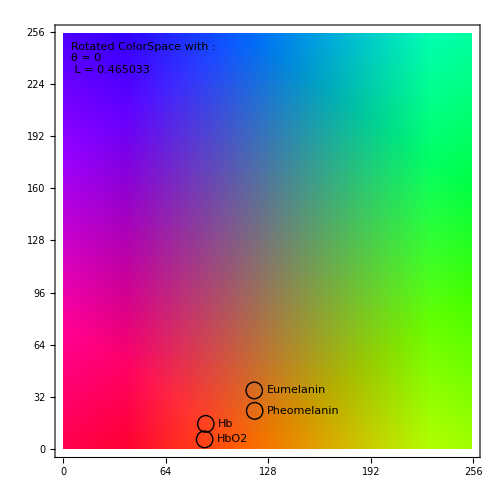
```mathematica
Clear[theoreticalValuesPlt];theoreticalValuesPlt=-Graphics-;
```

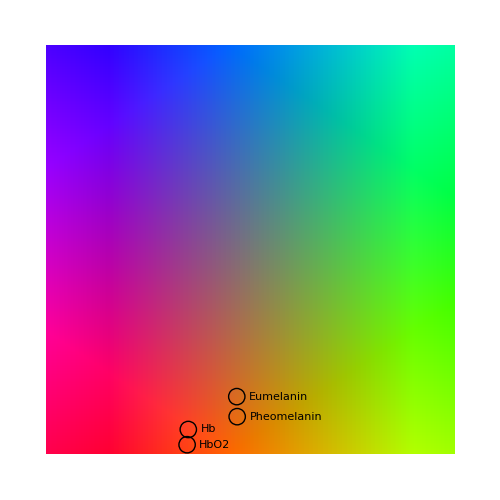
```mathematica
Clear[theoreticalValuesPltPlane];theoreticalValuesPltPlane=-Graphics-;
```

```mathematica
minCa=0;maxCa=255;
minCb=0;maxCb=255;
vtc={{0,0},{1,0},{1,1},{0,1}};
theoreticalValues3DPlt=Graphics3D[{Texture[theoreticalValuesPltPlane],Polygon[{{minCa,minCb,0},{maxCa,minCb,0},{maxCa,maxCb,0},{minCa,maxCb,0}},VertexTextureCoordinates->vtc]},Lighting->"Neutral"];
```

```mathematica
theoreticalValues3DPlt
```

-Graphics3D-

## Setup

```mathematica
Panel[Column[blobGet]]
```

BinSkinnedRotTopTailCaCbDespecblob2
BinSkinnedRotTopTailCaCbDespecblob1
RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1
RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBFSkinBinSkinnedRotTopTailCaCbDespecblob1
RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBJSkinBinSkinnedRotTopTailCaCbDespecblob1
RGBNSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBNSkinBinSkinnedRotTopTailCaCbDespecblob1

```mathematica
Panel[Row[{Panel[Column[Table[(Button["Move To Front #"<>ToString[i],blobs=BringToFront[blobs,{ii}];blobsFiles=BringToFront[blobsFiles,{ii}],Background->Dynamic[blobFitPlotColor[ii]]]//.ii->i),{i,1,Length[blobs]}]]],Dynamic[Panel[SwatchLegend[Table[blobFitPlotColor[i],{i,1,Length[blobs]}],Map[((StringSplit[Symbol[#]["PlotLabel"]," "])[[1]])&,blobs],LegendMarkers->"Bubble",LegendMarkerSize->16,LabelStyle->{GrayLevel[0.3],Bold,16}]]]}],"The Plot Order for the Sets"]
```

Move To Front #1
Move To Front #2
Move To Front #3
Move To Front #4
Move To Front #5The Plot Order for the Sets

```mathematica
figPath = $HomeDirectory <> "/Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter3/Figs/"
```

/Users/jaspershemilt/Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter3/Figs/

## Plots

```mathematica
outAllNextToEachOther3D = GraphicsRow[Table[Show[(Symbol[blobs[[i]]]["fitPlot"])[[1]],(Symbol[blobs[[i]]]["fitPlot"])[[2]],PlotLabel->Symbol[blobs[[i]]]["PlotLabel"] ],{i,1,Length[blobs]}],ImageSize->1000,Spacings->0];
Panel[Column[{Panel[outAllNextToEachOther3D
,Background->White,ImageSize->1000],
Button["Export",
Export[figPath<>"All_Next_To_Each_Other3D.jpg",outAllNextToEachOther3D,ImageResolution->300];
Export[figPath<>"All_Next_To_Each_Other3D.eps",outAllNextToEachOther3D];
Export[figPath<>"All_Next_To_Each_Other3D.pdf",outAllNextToEachOther3D]]}]]
```

-Graphics-
Export

```mathematica
margin=20;
rngs=Map[(OptionValue[Graphics3D,(Symbol[#]["fitPlot"])[[2]],PlotRange])&,blobs];
cmbRng={{Min[rngs[[All,1,1]]],Max[rngs[[All,1,2]]]}+{-margin,margin},{Min[rngs[[All,2,1]]],Max[rngs[[All,2,2]]]}+{-margin,margin},{Min[rngs[[All,3,1]]],Max[rngs[[All,3,2]]]} };

statTables=Map[Panel[Column[{Style[StringTake[Symbol[#]["PlotLabel"],{1,StringPosition[Symbol[#]["PlotLabel"]," ",1][[1,1]]}]
],Panel[statTable[Symbol[#],4,{1,2},Orientation-> "Vertical"],Background->White]}],Background->Symbol[#]["fitPlotColor"]]&,blobs];Panel[Column[{legend=SwatchLegend[Table[blobFitPlotColor[i],{i,1,Length[blobs]}],Map[((StringSplit[Symbol[#]["PlotLabel"]," "])[[1]])&,blobs],LegendMarkers->"Bubble",LegendMarkerSize->16,LabelStyle->{GrayLevel[0.3],Bold,16}];
outAllTogether3D = Grid[{{
Show[{theoreticalValues3DPlt,Map[((Symbol[#]["fitPlot"])[[1]])&,blobs]},PlotRange->cmbRng,Axes->True,AxesLabel->{"Ca","Cb",Column[{Style["Frequency",Bold],"f"},Alignment->Center]},ImageSize->1000,BoxRatios->{1,1,0.2},Epilog->Inset[legend,{Left,Top},{Left,Top}]]
,Column[{Sequence@@statTables}]}},Alignment->{Left,Top}];
Panel[outAllTogether3D ,Background->White],
Button["Export",
Export[figPath<>"All_Together_2D.jpg",outAllTogether2D,ImageResolution->300];
Export[figPath<>"All_Together_2D.eps",outAllTogether2D];
Export[figPath<>"All_Together_2D.pdf",outAllTogether2D]]}]]
```

-Graphics3D- | FJ&NSkin 
θ | 0.9312 | 
μ | Ca | 108.5
 | Cb | 86.86
σ | Ca' | 6.256
 | Cb' | 2.7
FSkin 
θ | 1.094 | 
μ | Ca | 109.1
 | Cb | 85.9
σ | Ca' | 6.719
 | Cb' | 2.023
JSkin 
θ | 0.8294 | 
μ | Ca | 104.
 | Cb | 85.56
σ | Ca' | 6.985
 | Cb' | 3.056
NSkin 
θ | 1.006 | 
μ | Ca | 110.1
 | Cb | 87.64
σ | Ca' | 5.473
 | Cb' | 2.788
GeneralSkin 
θ | 1.442 | 
μ | Ca | 123.1
 | Cb | 106.5
σ | Ca' | 5.161
 | Cb' | 1.183
Export

```mathematica
initColor=Map[(Symbol[#]["fitPlotColor"][[2]])&,blobs]
Panel[DynamicModule[{color=initColor,opcty=1,JSkinoutExport=Graphics3D[{Cuboid[{0,0,0},{255,255,255}]}],AxisLineThickness=4.0,EllipsLineThickness=4.0,sig={2,4},len=10,endSig=5,txtColor=initColor,txtOpacity=0,ellipsColor=initColor,ellipsOpacity=0.8,axisColor=initColor,axisOpacity=0.8,out2D=Graphics[{Rectangle[{0,0},{255,255}]}]},
Column[{
Row[{
Panel[Column[{
Grid[{
 {Style["Axis",  Bold],Table[ColorSetter[Dynamic[axisColor[[ii]]]]/.ii->i,{i,1,Length[axisColor]}],Slider[Dynamic[axisOpacity],{0,1}]},
{Style["Ellips",Bold],Table[ColorSetter[Dynamic[ellipsColor[[ii]]]]/.ii->i,{i,1,Length[ellipsColor]}] ,Slider[Dynamic[ellipsOpacity],{0,1}]},
{Style["Text",  Bold],Table[ColorSetter[Dynamic[txtColor[[ii]]]]/.ii->i,{i,1,Length[txtColor]}] ,Slider[Dynamic[txtOpacity],{0,1}]},
{Style["Sig",   Bold],Dynamic[sig],IntervalSlider[Dynamic[sig],{1,10,1}]},
{Style["len",   Bold],Dynamic[len],Slider[Dynamic[len],{1,10,1}]},
{Style["Ellipse Thick",Bold],Dynamic[EllipsLineThickness],Slider[Dynamic[EllipsLineThickness],{0,25}]},
{Style["Axis Thick",Bold],Dynamic[AxisLineThickness],Slider[Dynamic[AxisLineThickness],{0,25}]}}],
Button["Generate",Map[(Symbol[#]["overlayElems"]=.;)&,blobs];
Table[blob=blobs[[i]];
(Evaluate[Symbol[blob]["overlayElems"]]=overlayElems[Symbol[blob],{1,2},
AxisColor-> {Directive[AbsoluteThickness[AxisLineThickness],Opacity[axisOpacity],axisColor[[i]]],Directive[Opacity[axisOpacity],axisColor[[i]]]}, 
TextColor->Directive[Opacity[txtOpacity],txtColor[[i]]],
MeanColor->Blue,PointSize-> 0.5,
EllipsColor-> Directive[AbsoluteThickness[EllipsLineThickness],Opacity[ellipsOpacity],ellipsColor[[i]]],
EllipsisSigma->sig,AxisSigma->len]),{i,1,Length[blobs]}];
out2D=Show[Map[((Symbol[#]["overlayElems"])[[1,{1,2}]])&,blobs],(Symbol[blobs[[1]]]["overlayElems"])[[2]]]
],
Panel[Dynamic[out2D],Background->White]
}]]}],
Button["Save",Do[Save[blobsFiles[[i]],blobs[[i]]],{i,1,Length[blobs]}]]
}]
]
]
```

{}

```mathematica
Map[(Symbol[#]["overlayElems"]=Symbol[#]["overlayElems"] /.{Thickness[_]->AbsoluteThickness[4]})&,blobs]
Map[(Symbol[#]["overlayElems"]=Symbol[#]["overlayElems"] /.{Opacity[_]->Opacity[0.8]})&,blobs]
```

```mathematica
blobs
```

{BinSkinnedRotTopTailCaCbDespecblob2,RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBNSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1}

```mathematica
BinSkinnedRotTopTailCaCbDespecblob2["PlotLabel"] = "FJ&NSkin CaCb Bin Blob1"
```

FJ&NSkin CaCb Bin Blob1

```mathematica
statTables=Map[Panel[Column[{Style[StringTake[Symbol[#]["PlotLabel"],{1,StringPosition[Symbol[#]["PlotLabel"]," ",1][[1,1]]}]
],Panel[statTable[Symbol[#],4,{1,2},Orientation-> "Vertical"],Background->White]}],Background->Symbol[#]["fitPlotColor"]]&,blobs];
Panel[Column[{legend=SwatchLegend[Table[blobFitPlotColor[i],{i,1,Length[blobs]}],Map[((StringSplit[Symbol[#]["PlotLabel"]," "])[[1]])&,blobs],LegendMarkers->"Bubble",LegendMarkerSize->16,LabelStyle->{GrayLevel[0.3],Bold,16}];
outAllTogether2D = Grid[{{Show[{theoreticalValuesPlt,Graphics[{Circle[{128,128},1]}],Map[({Symbol[#]["overlayElems"][[1,2]],Symbol[#]["overlayElems"][[1,1]]} /.RGBColor[_,_,_]->RGBColor[1,1,1])&,Reverse[blobs]],Map[({Symbol[#]["overlayElems"][[1,2]],Symbol[#]["overlayElems"][[1,1]]} )&,Reverse[blobs]]},ImageSize->700,Axes->True,AxesLabel->{"Ca","Cb"},Epilog->Inset[legend,{250,250},{Right,Top}]],Column[{Sequence@@statTables}]}},Alignment->{Left,Center}];
Panel[outAllTogether2D ,Background->White],
Button["Export",
Export[figPath<>"All_Together_2D.jpg",outAllTogether2D,ImageResolution->300];
Export[figPath<>"All_Together_2D.eps",outAllTogether2D];
Export[figPath<>"All_Together_2D.pdf",outAllTogether2D]]}]]
```

-Graphics- | FJ&NSkin 
θ | 0.9312 | 
μ | Ca | 108.5
 | Cb | 86.86
σ | Ca' | 6.256
 | Cb' | 2.7
FSkin 
θ | 1.094 | 
μ | Ca | 109.1
 | Cb | 85.9
σ | Ca' | 6.719
 | Cb' | 2.023
JSkin 
θ | 0.8294 | 
μ | Ca | 104.
 | Cb | 85.56
σ | Ca' | 6.985
 | Cb' | 3.056
NSkin 
θ | 1.006 | 
μ | Ca | 110.1
 | Cb | 87.64
σ | Ca' | 5.473
 | Cb' | 2.788
GeneralSkin 
θ | 1.442 | 
μ | Ca | 123.1
 | Cb | 106.5
σ | Ca' | 5.161
 | Cb' | 1.183
Export

```mathematica
accuracy=0.00005;
FJNθ=0.9311568907247014;Fθ=1.094; Jθ=0.8294; Nθ=1.006;
```

```mathematica
Grid[Transpose[{Map[Style[#,Bold]&,{"Set","FJ&NSkin θ_FJN","FSkin θ_F","JSkin θ_J","NSkin θ_N"}],Prepend[Map[(NumberForm[(#),{4,4}])&,{FJNθ,Fθ,Jθ,Nθ}],Style["Decimal",Bold]],Prepend[Map[(Rationalize[(#)/Pi,accuracy]Pi)&,{FJNθ,Fθ,Jθ,Nθ}],Style["Approx",Bold]],Prepend[Map[("θ_FJN"-Rationalize[(#)/Pi,0.0005]Pi)&,{0,FJNθ-Fθ,FJNθ-Jθ,FJNθ-Nθ}],Style["Relative",Bold]]}],Frame->All]
```

Set | Decimal | Approx | Relative
FJ&NSkin θ_FJN | 0.9312 | (75 π)/253 | θ_FJN
FSkin θ_F | 1.0940 | (39 π)/112 | θ_FJN+(3 π)/58
JSkin θ_J | 0.8294 | (33 π)/125 | θ_FJN-π/31
NSkin θ_N | 1.0060 | (49 π)/153 | θ_FJN+π/42

This suggests that taking θ’ to be in the range θ_FJN-π/84 < θ’ < θ_FJN+π/84 is safe as it is at most half way to the nearest individual. This is arbitary and we could extend the region is we had reason but this range is sufficient to ensure that a computationally advantagious value will be within the range being 1/7 th of a Pi/6 region.

The choice of θ’ affects the position of the mean value μ’

```mathematica
μ=BinSkinnedRotTopTailCaCbDespecblob2["gMean"];
μp=N[RotationMatrix[-FJNθ] . (μ-{128,128})+ {128,128}];
σ=BinSkinnedRotTopTailCaCbDespecblob2["gSigma"];
Block[{digits=3},
Grid[{{Style["θ'", Bold], NumberForm[FJNθ, digits], SpanFromLeft}, {Style["μ'", Bold], "Ca'", NumberForm[μp[[1]], digits]}, 
        {SpanFromAbove, "Cb'", NumberForm[μp[[2]], digits]}, {Style["σ", Bold], "Ca'", NumberForm[σ[[1]], digits]}, 
        {SpanFromAbove, "Cb'", NumberForm[σ[[2]], digits]}}, Frame -> All, Alignment -> {Center, Center}, Background -> RGBColor[1, 1, 1, 0.6]]
]
```

θ' | 0.931 | 
μ' | Ca' | 83.4
 | Cb' | 119.
σ | Ca' | 6.26
 | Cb' | 2.7

```mathematica
θp=0.9311568907247014;
μp = {83.37287378467443,119.05707430077418};
σ = {6.256349617020853,2.6995505283053283};
```

```mathematica
μpLimits=Round[{N[RotationMatrix[-FJNθ+π/84] . (μ-{128,128}) + {128,128}],N[RotationMatrix[-FJNθ] . (μ-{128,128})+ {128,128}],N[RotationMatrix[-FJNθ-π/84] . (μ-{128,128})+ {128,128}]}];
Row[{MatrixForm[μpLimits[[1]]]," < μ' < ",MatrixForm[μpLimits[[3]]]}]
Grid[{Prepend[Map[("θ_FJN"+#)&,{-π/84,0,π/84}],Style["θ' ",Bold]], Prepend[Map[MatrixForm,μpLimits],Style["μ' ",Bold]]},Frame->All]
```

(84
117) < μ' < (83
121)

θ'  | θ_FJN-π/84 | θ_FJN | θ_FJN+π/84
μ'  | (84
117) | (83
119) | (83
121)

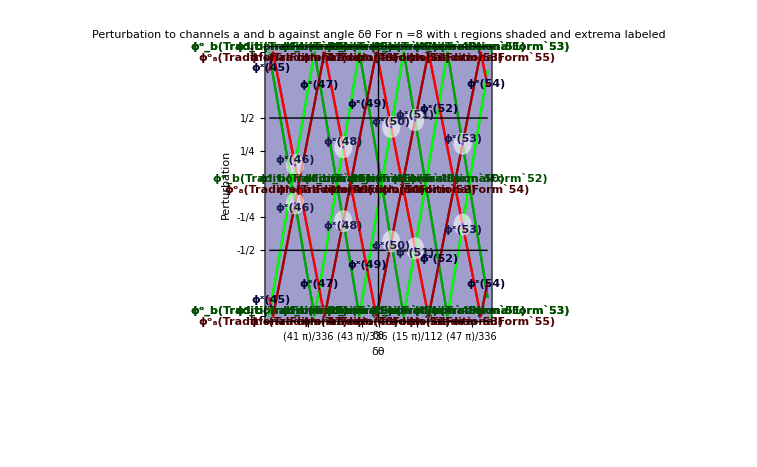
-Graphics- | θ | Θ | δθ | τ
0.9312 | π/6 | 0.4076 | 1/2θ = Θ + δθ
+21.00° < θ' < +25.00°Acceptable Values for θ'
 | θ' | Perturbation | Change in θ
ϕ^x(46) | 0.9026 | ±0.1441 | -1.6380°
ϕ^x(48) | 0.9191 | ±0.2791 | -0.6914°
ϕ^x(50) | 0.9355 | ±0.4320 | +0.2496°
ϕ^x(51) | 0.9437 | ±0.4848 | +0.7181°
ϕ^x(53) | 0.9600 | ±0.3051 | +1.6500°Values of θ which produce a perturbation less than τ

```mathematica
perturbationPlot[FJNθ,1/2,8,PlotRange->{Mod[FJNθ,Pi/6]-(Pi/84),Mod[FJNθ,Pi/6] + (Pi/84)}]
```

Choose thetaIntersection[46, 8] within 2 degrees or (Pi/84) of θ and very low error.

```mathematica
θFinal=Simplify[Quotient[theta,Pi/6] Pi/6 +thetaIntersection[46,8][[1]]];
μFinal = {108.53679981821153,86.85707651388756};
σFinal = {6.256349617020853,2.6995505283053283};
Row[{"θ' = ",ntheta," = ",NumberForm[N[θFinal],16]}]
Row[{"μ = ",NumberForm[N[μFinal],{4,1}]}]
Row[{"σ = ",NumberForm[N[σFinal],4]}]
```

θ' = π/6+ArcTan[(-89+13 √73)/(32 √3)] = 0.902576829326826

μ = {108.5,86.9}

σ = {6.256,2.7}

Find the 5 sigma cube

```mathematica
Clear[val]
Block[{θ, R}, θ = θFinal; R = Simplify[RotationMatrix[θ, {1, 0, 0}] . RotationMatrix[-ArcTan[1/Sqrt[2]], {0, 0, 1}] . RotationMatrix[Pi/4, {0, 1, 0}]]; 
   toLCaCbFinal = Function[{val}, rrR . val*{1/Sqrt[3], Sqrt[3/8], 1/Sqrt[2]} + {0, 0.5, 0.5}] /. 
     {rrR -> Simplify[RotationMatrix[θ, {1, 0, 0}] . RotationMatrix[-ArcTan[1/Sqrt[2]], {0, 0, 1}] . RotationMatrix[Pi/4, {0, 1, 0}]]}; 
   fromLCaCbFinal = Function[{val}, iR . ((val - {0, 0.5, 0.5})*{Sqrt[3], 2*Sqrt[2/3], Sqrt[2]})] /. {iR -> Inverse[R]}; ]
```

```mathematica
LCaCbFiveSquare=Map[Prepend[#,128]&,Map[(μFinal+5 σFinal#)&,{{-1,-1},{1,-1},{1,1},{-1,1}}]];
RGBFiveSquare=Map[Round[255 fromLCaCbFinal[#/255]]&,LCaCbFiveSquare]
```

{{161,37,185},{192,89,103},{163,114,107},{132,62,190}}

```mathematica
RGBFiveCube={Sequence@@Map[(#+(255-Max[#]))&,RGBFiveSquare],
Sequence@@Map[(#-(Min[#]))&,RGBFiveSquare]};
Table[{Min[RGBFiveCube[[All,i]]],Max[RGBFiveCube[[All,i]]]},{i,1,3}]
```

{{56,255},{0,206},{0,255}}

```mathematica
BinSkinnedRotTopTailCaCbDespecblob2["gTheta"]
BinSkinnedRotTopTailCaCbDespecblob2["gMean"]
BinSkinnedRotTopTailCaCbDespecblob2["gSigma"]
```

0.931157

{108.537,86.8571}

{6.25635,2.69955}

#### Save the color Definitions

```mathematica
Map[(CellPrint[Cell[BoxData[RowBox[{(StringReplace[(StringSplit[Symbol[#]["PlotLabel"]," "])[[1]],"&"->""])<>"InitColor","=",ToBoxes[(Symbol[#]["fitPlotColor"])[[2]],StandardForm],";"}]],"Code",InitializationCell->True]])&,blobs]
```

```mathematica
blobs
```

{BinSkinnedRotTopTailCaCbDespecblob2,RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBNSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1}

WhiteOut and Blackout

#### Init

```mathematica
Clear[rgbCubeInLCaCb]
rgbCubeInLCaCb[scale_:1,θ_:0]:=Translate[GeometricTransformation[Rotate[Rotate[Rotate[{EdgeForm[Black],FaceForm[],Cuboid[{0,0,0},{scale,scale,scale}]},Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],θ,{1,0,0}],ScalingMatrix[{1/(√3),√(3/8),1/(√2)}]],{0,0.5 scale,0.5 scale}];

Graphics3D[{Opacity[0.2],rgbCubeInLCaCb[1]},ViewVertical->{1, 0, 0},Axes->True,AxesLabel->{"L","Ca","Cb"}]
```

-Graphics3D-

```mathematica
Clear[val]
Block[{θ,R},
θ=0;
R=Simplify[RotationMatrix[θ,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[Pi/4,{0,1,0}]];

toLCaCb=Function[{val},((rrR . val) {1/(√3),√(3/8),1/(√2)})+{0,0.5,0.5}]/.{rrR-> Simplify[RotationMatrix[θ,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[Pi/4,{0,1,0}]]};
fromLCaCb=Function[{val},iR . ((val -{0,0.5,0.5}) {√3,2 √(2/3),√2}) ]/.{iR->Inverse[R]};
]
```

```mathematica
Clear[WOBOPathLCaCb]
WOBOPathLCaCb[rgb:{_,_,_},scale_:1]:=Module[{ordering,sc},
sc=N[1/128];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
scale {
toLCaCb[{0,0,0}],
toLCaCb[ReplacePart[rgb-b,{ordering[[1]]->0,ordering[[2]]->0}]],
toLCaCb[(rgb-a)],
toLCaCb[(rgb+(1-c))],
toLCaCb[(ReplacePart[rgb+(1-b),{ordering[[3]]->1,ordering[[2]]->1}])],
toLCaCb[({1,1,1})]}
]
```

```mathematica
WOBOTubePathLCaCb[rgb:{_,_,_},scale_:1]:=Module[{color,ordering,sc},
sc=scale N[1/128];
color=RGBColor[rgb];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
{FaceForm[color,color],EdgeForm[],
Tube[ WOBOPathLCaCb[rgb,scale]
,sc]
}]
```

```mathematica
WOBOTubePath[rgb:{_,_,_},scale_:1]:=Module[{color,ordering,sc},
sc=scale N[1/128];
color=RGBColor[rgb];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
{FaceForm[color,color],EdgeForm[],
Tube[ WOBOPath[rgb,scale]
,sc]
}]
```

```mathematica
WOBOPath[rgb:{_,_,_},scale_:1]:=Module[{ordering},
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
scale {
{0,0,0},
ReplacePart[rgb-b,{ordering[[1]]->0,ordering[[2]]->0}],
rgb-a,
rgb+(1-c),
ReplacePart[rgb+(1-b),{ordering[[3]]->1,ordering[[2]]->1}],
{1,1,1}
}]
```

```mathematica
colorPath[path_,disc_:N[1/256]]:=Module[{},
Table[
vec=path[[j+1]]-path[[j]];
 dist=Max[vec];
Table[
RGBColor[path[[j]]+i  vec/dist],{i,0,dist,disc}]
,{j,1,Length[path]-1}]
]
```

```mathematica
normColor[RGBColor[{r_,g_,b_}],bright_:0.5]:=Module[{lum},lum=3 bright ;
brighten=(lum-r-g-b)/3;
RGBColor[r+brighten,g+ brighten,b+ brighten]
]
```

```mathematica
Clear[WOBOColorEffect]
Options[WOBOColorEffect]=Flatten[{TickNames->{"Black","λ_B^Sat","λ_B","λ_W","λ_W^Sat","White"},Normed->True,TextInGraphic->False,Options[Graphics]}];
WOBOColorEffect[rgb_List,opts:OptionsPattern[]]:=Module[{ticks,ht,hta,path,clrPath,normClrPath,lens,starts,aspect,strip,txtShift,txtAlign},
ticks=OptionValue[TickNames];(*{"Black","λ_B^Sat","λ_B","λ_W","λ_W^Sat","White"};*)
aspect=1/7;
path=WOBOPath[rgb];
clrPath=colorPath[path];
normClrPath=Map[normColor,clrPath,{2} ];
lens=Map[Length,normClrPath];
starts=Table[Total[lens[[1;;i]]],{i,0,Length[lens]}];
ht=aspect starts[[-1]];
hta=aspect starts[[-1]]/6;
If[TrueQ[OptionValue[TextInGraphic]],txtShift=2;txtAlign={Center,Center},txtShift=1;txtAlign={Left,Center}];
If[OptionValue[Normed],
strip={Table[{Table[{normClrPath[[j,i]],Rectangle[{i+starts[[j]],0},{i+starts[[j]]+1,ht}]},{i,1,Length[normClrPath[[j]]]}]},{j,1,Length[normClrPath]}],Text["Brightness Adjusted Color",{(hta+starts[[-1]])/txtShift, ht/2},txtAlign]},
strip={Table[{Table[{clrPath[[j,i]],Rectangle[{i+starts[[j]],0},{i+starts[[j]]+1,ht}]},{i,1,Length[clrPath[[j]]]}]},{j,1,Length[clrPath]}],Text["Detected Color"  ,{(hta+starts[[-1]])/txtShift,ht/2},txtAlign]},
strip ={Table[{Table[{
normClrPath[[j,i]],Rectangle[{i+starts[[j]],ht/2+hta/2 },{i+starts[[j]]+1,ht    }],
clrPath[[j,i]],         Rectangle[{i+starts[[j]],0        },{i+starts[[j]]+1,ht/2-hta/2}]},{i,1,Length[normClrPath[[j]]]}]},{j,1,Length[normClrPath]}],
Text["Detected Color"  ,{(hta+starts[[-1]])/txtShift,ht/4},txtAlign],Text["Brightness Adjusted Color",{(hta+starts[[-1]])/txtShift,3 ht/4},txtAlign]}
];
Graphics[{
Table[{Black,Rectangle[{1+starts[[j]],-5},{2+starts[[j]],ht+hta}],Text[ticks[[j]],{1+starts[[j]],ht+hta},{Center,Bottom}]},{j,{1,3,4,6}}],
Table[{Black,Rectangle[{1+starts[[j]],-5},{2+starts[[j]],ht+hta}],Text[ticks[[j]],{1+starts[[j]],-hta},{Center,Top}]},{j,{2,5}}],,
strip},FilterRules[{opts},Options[Graphics]]]
]
```

#### WOBO Plots

```mathematica
lines=Table[
μ=Symbol[blobs[[blob]]]["gMean"]/256;
σ=Symbol[blobs[[blob]]]["gSigma"]/256;
θ=Symbol[blobs[[blob]]]["gTheta"];
Table[val=GaussianFitFun[Ca,Cb,μ,σ,θ];{Opacity[val],If[val>0.05,WOBOTubePathLCaCb[fromLCaCb[{0.5,Ca,Cb}]],Sequence[]]},
{Ca,μ[[1]]-3 σ[[1]],μ[[1]]+3 σ[[1]],1/128},{Cb,μ[[2]]-3 σ[[2]],μ[[2]]+3 σ[[2]],1/128}],
{blob,1,Length[blobs]}];

colors=Table[
μ=Symbol[blobs[[blob]]]["gMean"]/256;
σ=Symbol[blobs[[blob]]]["gSigma"]/256;
θ=Symbol[blobs[[blob]]]["gTheta"];
colors=WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->350,Normed->True,TextInGraphic->True],
{blob,1,Length[blobs]}];
cube=Graphics3D[{rgbCubeInLCaCb[],lines},ViewVertical->{1,0,0},Axes->True,AxesLabel->{"L","Ca","Cb"},Lighting->{{"Ambient",White}},ImageSize->500];
Grid[{{cube,Column[colors]}},Alignment->Left]
```

```mathematica
blob=3;
μ=Symbol[blobs[[blob]]]["gMean"]/256;
σ=Symbol[blobs[[blob]]]["gSigma"]/256;
θ=Symbol[blobs[[blob]]]["gTheta"];
stat=Panel[Column[{Style[StringTake[Symbol[blobs[[blob]]]["PlotLabel"],{1,StringPosition[Symbol[blobs[[blob]]]["PlotLabel"]," ",1][[1,1]]}]],Panel[statTable[Symbol[blobs[[blob]]],4,{1,2},Orientation-> "Vertical"],Background->White],Panel[Grid[Transpose[{{"","Black","λ_B^Sat","λ_B","λ_W","λ_W^Sat","White"},Flatten[{"0-1",Map[(NumberForm[#,3])&,N[(WOBOPathLCaCb[fromLCaCb[{0.5,μ[[1]],μ[[2]]}]])][[All,1]]]}],Flatten[{"0-255",Round[N[255(WOBOPathLCaCb[fromLCaCb[{0.5,μ[[1]],μ[[2]]}]])][[All,1]]]}]}], Frame->All,Alignment->{Center,Center}],Background->White]}],Background->Lighter[(Symbol[blobs[[blob]]]["fitPlotColor"])[[2]],0.7]];
lines=Table[val=GaussianFitFun[Ca,Cb,μ,σ,θ];{Opacity[val],If[val>0.05,WOBOTubePathLCaCb[fromLCaCb[{0.5,Ca,Cb}]],Sequence[]]},
{Ca,μ[[1]]-2 σ[[1]],μ[[1]]+3 σ[[1]],1/128},{Cb,μ[[2]]-2 σ[[2]],μ[[2]]+3 σ[[2]],1/128}];
cube=Graphics3D[{rgbCubeInLCaCb[],lines},ViewVertical->{1,0,0},Axes->True,AxesLabel->{"L","Ca","Cb"},ImageSize->500,Lighting->{{"Ambient",White}},ViewPoint->{1.3,3.9,2}];
colorsNorm  =WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->700,Normed->True,TextInGraphic->True];
colorsDtctd=WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->700,Normed->False,TextInGraphic->True];
colors=WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->700,Normed->"Both"];
Panel[Grid[{
{colorsDtctd,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{stat,Panel[cube,Background->White],SpanFromLeft,SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromAbove,SpanFromBoth,SpanFromBoth,SpanFromBoth},
{SpanFromAbove,SpanFromAbove,SpanFromBoth,SpanFromBoth,SpanFromBoth},
{colorsNorm,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft}
},Alignment->{Left,Top}],FrameMargins->5]
```

#### WhitePoint Plots

```mathematica
Graphics3D[{rgbCubeInLCaCb[1],Table[WOBOTubePathLCaCb[ReplacePart[toLCaCb[{RandomReal[],RandomReal[],RandomReal[]}],1->0.5]],{i,1,200}]},ViewVertical->{1,0,0},Axes->True]
```

Generate a new sample set with nBlobs colors. Generate the pallets then display and photograph to generate the new set.

```mathematica
WOBOpathBase="/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/";
```

```mathematica
nBlobs=6;
startColors=Table[{RandomReal[{0,0.95}],RandomReal[{0,0.95}],RandomReal[{0,0.95}]},{i,1,nBlobs}];
theoryColorsLCaCb={rgbCubeInLCaCb[255],Table[WOBOTubePathLCaCb[startColors[[i]],255]/.{Tube[{_,_,a_,b_,_,_},r_]:> Tube[{a,b},r]},{i,1,Length[startColors]}]};
theoryColorsRGB={Table[WOBOTubePath[startColors[[i]],255]/.{Tube[{_,_,a_,b_,_,_},r_]:> Tube[{a,b},r]},{i,1,Length[startColors]}]};
Row[{Graphics3D[theoryColorsLCaCb,ViewVertical->{1,0,0},Axes->True,ViewPoint->{Infinity,0,0},ImageSize->400],
Graphics3D[theoryColorsRGB,ViewVertical->{1,0,0},Axes->True,ImageSize->400]}]
```

```mathematica
WOBOpath=WOBOpathBase<>"WhitePoint/"<>FromCharacterCode[Table[RandomInteger[Flatten[{ToCharacterCode["A"],ToCharacterCode["Z"]}]],{i,1,10}]]<>"/"
Quiet[CreateDirectory[WOBOpath],CreateDirectory::filex];
Quiet[CreateDirectory[WOBOpath<>"src/"],CreateDirectory::filex];
Quiet[CreateDirectory[WOBOpath<>"figs/"],CreateDirectory::filex];
Save[WOBOpath<>"startColors.m",startColors];
paths=Map[WOBOPath,startColors][[All,{3,4}]];
colors=Map[((colorPath[#,N[1/256]])[[1]])&,paths];
selLen=Min[{Min[Map[Length,colors]],42}];
selection=(Table[Sequence@@(Map[RandomSample[#,selLen]&,colors]),{i,1,Ceiling[24/nBlobs]}]);
panels=Table[GraphicsGrid[ArrayReshape[Map[(Graphics[{#,Rectangle[]}])&,selection[[All,i]] ],{4,6}],ImageSize->Full,Background->Black],{i,1,selLen}];
theoryColors=Graphics3D[{rgbCubeInLCaCb[1],Table[WOBOTubePathLCaCb[startColors[[i]]]/.{Tube[{_,_,a_,b_,_,_},r_]:> Tube[{a,b},r]},{i,1,Length[startColors]}]},ViewVertical->{1,0,0},Axes->True];
Do[
Export[WOBOpath<>"src/Panel"<>ToString[i]<>".jpg",panels[[i]],ImageResolution->300];
,{i,1,selLen}]
Export[WOBOpath<>"figs/TheoreticalDisrto.jpg",theoryColors,ImageResolution->300 ]
```

```mathematica
theoryColorsLCaCb={rgbCubeInLCaCb[255],Table[WOBOTubePathLCaCb[startColors[[i]],255]/.{Tube[{_,_,a_,b_,_,_},r_]:> Tube[{a,b},r]},{i,1,Length[startColors]}]};
theoryColorsRGB={Table[WOBOTubePath[startColors[[i]],255]/.{Tube[{_,_,a_,b_,_,_},r_]:> Tube[{a,b},r]},{i,1,Length[startColors]}]};
Graphics3D[theoryColorsLCaCb,ViewVertical->{1,0,0},Axes->True,ViewPoint->{Infinity,0,0}]
Graphics3D[theoryColorsRGB,ViewVertical->{1,0,0},Axes->True]
```

```mathematica
Show[theoryColors,ViewPoint->{Infinity,0,0}]
```

```mathematica
Graphics3D[{Black,Cuboid[{0,0,0},{1,1,1}],Table[WOBOPath[{RandomReal[],RandomReal[],RandomReal[]}],{i,1,200}]},ViewVertical->{1,1,1}]
```

```mathematica
R=Simplify[RotationMatrix[Pi/4,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[0,{0,1,0}]]
```

```mathematica
cube=Flatten[{EdgeForm[Black],FaceForm[],Cuboid[{0,0,0},{1,1,1}],Table[WOBOPath[{RandomReal[],RandomReal[],RandomReal[]}],{i,1,200}]}];
cubeRot=Normal@Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],Pi/4,{1,0,0}];
```

```mathematica
Graphics3D[cubeRot,ViewVertical->{1, 0, 0},Axes->True]
```

```mathematica
Graphics3D[GeometricTransformation[cubeRot,ScalingMatrix[{1/(√3),√(3/8),1/(√2)}]],AspectRatio->1]
```